```mathematica
σ0[r_]:=Piecewise[{{0.7218327782044995 BSplineBasis[{3,{-0.15700261970979576,-0.10466841313986384,-0.05233420656993192,0.,0.05233420656993192}},0,r]+0.7218027564723335 BSplineBasis[{3,{-0.10466841313986384,-0.05233420656993192,0.,0.05233420656993192,0.10466841313986384}},0,r]+0.7218327782044995 BSplineBasis[{3,{-0.05233420656993192,0.,0.05233420656993192,0.10466841313986384,0.15700261970979576}},0,r]+0.7219228181454528 BSplineBasis[{3,{0.,0.05233420656993192,0.10466841313986384,0.15700261970979576,0.2093368262797277}},0,r]+0.7220727837516223 BSplineBasis[{3,{0.05233420656993192,0.10466841313986384,0.15700261970979576,0.2093368262797277,0.2616710328496596}},0,r]+0.722282523813766 BSplineBasis[{3,{0.10466841313986384,0.15700261970979576,0.2093368262797277,0.2616710328496596,0.3140052394195915}},0,r]+0.7225518271069111 BSplineBasis[{3,{0.15700261970979576,0.2093368262797277,0.2616710328496596,0.3140052394195915,0.36633944598952345}},0,r]+0.7228804228560326 BSplineBasis[{3,{0.2093368262797277,0.2616710328496596,0.3140052394195915,0.36633944598952345,0.4186736525594554}},0,r]+0.72326798133186 BSplineBasis[{3,{0.2616710328496596,0.3140052394195915,0.36633944598952345,0.4186736525594554,0.4710078591293873}},0,r]+0.7237141145745432 BSplineBasis[{3,{0.3140052394195915,0.36633944598952345,0.4186736525594554,0.4710078591293873,0.5233420656993192}},0,r]+0.7242183772424757 BSplineBasis[{3,{0.36633944598952345,0.4186736525594554,0.4710078591293873,0.5233420656993192,0.5756762722692511}},0,r]+0.7247802675831324 BSplineBasis[{3,{0.4186736525594554,0.4710078591293873,0.5233420656993192,0.5756762722692511,0.628010478839183}},0,r]+0.7253992285223343 BSplineBasis[{3,{0.4710078591293873,0.5233420656993192,0.5756762722692511,0.628010478839183,0.680344685409115}},0,r]+0.7260746488679435 BSplineBasis[{3,{0.5233420656993192,0.5756762722692511,0.628010478839183,0.680344685409115,0.7326788919790469}},0,r]+0.7268058646235921 BSplineBasis[{3,{0.5756762722692511,0.628010478839183,0.680344685409115,0.7326788919790469,0.7850130985489788}},0,r]+0.7275921604076798 BSplineBasis[{3,{0.628010478839183,0.680344685409115,0.7326788919790469,0.7850130985489788,0.8373473051189108}},0,r]+0.7284327709725272 BSplineBasis[{3,{0.680344685409115,0.7326788919790469,0.7850130985489788,0.8373473051189108,0.8896815116888427}},0,r]+0.7293268828182564 BSplineBasis[{3,{0.7326788919790469,0.7850130985489788,0.8373473051189108,0.8896815116888427,0.9420157182587746}},0,r]+0.7302736358956776 BSplineBasis[{3,{0.7850130985489788,0.8373473051189108,0.8896815116888427,0.9420157182587746,0.9943499248287065}},0,r]+0.7312721253922024 BSplineBasis[{3,{0.8373473051189108,0.8896815116888427,0.9420157182587746,0.9943499248287065,1.0466841313986384}},0,r]+0.7323214035945765 BSplineBasis[{3,{0.8896815116888427,0.9420157182587746,0.9943499248287065,1.0466841313986384,1.0990183379685703}},0,r]+0.7334204818220241 BSplineBasis[{3,{0.9420157182587746,0.9943499248287065,1.0466841313986384,1.0990183379685703,1.1513525445385022}},0,r]+0.7345683324232359 BSplineBasis[{3,{0.9943499248287065,1.0466841313986384,1.0990183379685703,1.1513525445385022,1.2036867511084341}},0,r]+0.7357638908304973 BSplineBasis[{3,{1.0466841313986384,1.0990183379685703,1.1513525445385022,1.2036867511084341,1.256020957678366}},0,r]+0.7370060576641534 BSplineBasis[{3,{1.0990183379685703,1.1513525445385022,1.2036867511084341,1.256020957678366,1.308355164248298}},0,r]+0.7382937008805459 BSplineBasis[{3,{1.1513525445385022,1.2036867511084341,1.256020957678366,1.308355164248298,1.36068937081823}},0,r]+0.7396256579565157 BSplineBasis[{3,{1.2036867511084341,1.256020957678366,1.308355164248298,1.36068937081823,1.4130235773881619}},0,r]+0.7410007381035687 BSplineBasis[{3,{1.256020957678366,1.308355164248298,1.36068937081823,1.4130235773881619,1.4653577839580938}},0,r]+0.7424177245048276 BSplineBasis[{3,{1.308355164248298,1.36068937081823,1.4130235773881619,1.4653577839580938,1.5176919905280257}},0,r]+0.7438753765679544 BSplineBasis[{3,{1.36068937081823,1.4130235773881619,1.4653577839580938,1.5176919905280257,1.5700261970979577}},0,r]+0.745372432187315 BSplineBasis[{3,{1.4130235773881619,1.4653577839580938,1.5176919905280257,1.5700261970979577,1.6223604036678896}},0,r]+0.7469076100087751 BSplineBasis[{3,{1.4653577839580938,1.5176919905280257,1.5700261970979577,1.6223604036678896,1.6746946102378215}},0,r]+0.7484796116906615 BSplineBasis[{3,{1.5176919905280257,1.5700261970979577,1.6223604036678896,1.6746946102378215,1.7270288168077534}},0,r]+0.7500871241545876 BSplineBasis[{3,{1.5700261970979577,1.6223604036678896,1.6746946102378215,1.7270288168077534,1.7793630233776854}},0,r]+0.7517288218200405 BSplineBasis[{3,{1.6223604036678896,1.6746946102378215,1.7270288168077534,1.7793630233776854,1.8316972299476173}},0,r]+0.7534033688168362 BSplineBasis[{3,{1.6746946102378215,1.7270288168077534,1.7793630233776854,1.8316972299476173,1.8840314365175492}},0,r]+0.7551094211697866 BSplineBasis[{3,{1.7270288168077534,1.7793630233776854,1.8316972299476173,1.8840314365175492,1.9363656430874812}},0,r]+0.7568456289501753 BSplineBasis[{3,{1.7793630233776854,1.8316972299476173,1.8840314365175492,1.9363656430874812,1.988699849657413}},0,r]+0.7586106383889056 BSplineBasis[{3,{1.8316972299476173,1.8840314365175492,1.9363656430874812,1.988699849657413,2.041034056227345}},0,r]+0.7604030939464735 BSplineBasis[{3,{1.8840314365175492,1.9363656430874812,1.988699849657413,2.041034056227345,2.0933682627972767}},0,r]+0.7622216403352053 BSplineBasis[{3,{1.9363656430874812,1.988699849657413,2.041034056227345,2.0933682627972767,2.1457024693672087}},0,r]+0.7640649244895171 BSplineBasis[{3,{1.988699849657413,2.041034056227345,2.0933682627972767,2.1457024693672087,2.1980366759371406}},0,r]+0.7659315974802571 BSplineBasis[{3,{2.041034056227345,2.0933682627972767,2.1457024693672087,2.1980366759371406,2.2503708825070725}},0,r]+0.7678203163695223 BSplineBasis[{3,{2.0933682627972767,2.1457024693672087,2.1980366759371406,2.2503708825070725,2.3027050890770044}},0,r]+0.7697297460026614 BSplineBasis[{3,{2.1457024693672087,2.1980366759371406,2.2503708825070725,2.3027050890770044,2.3550392956469364}},0,r]+0.771658560734505 BSplineBasis[{3,{2.1980366759371406,2.2503708825070725,2.3027050890770044,2.3550392956469364,2.4073735022168683}},0,r]+0.7736054460871936 BSplineBasis[{3,{2.2503708825070725,2.3027050890770044,2.3550392956469364,2.4073735022168683,2.4597077087868002}},0,r]+0.7755691003373063 BSplineBasis[{3,{2.3027050890770044,2.3550392956469364,2.4073735022168683,2.4597077087868002,2.512041915356732}},0,r]+0.77754823603031 BSplineBasis[{3,{2.3550392956469364,2.4073735022168683,2.4597077087868002,2.512041915356732,2.564376121926664}},0,r]+0.7795415814206799 BSplineBasis[{3,{2.4073735022168683,2.4597077087868002,2.512041915356732,2.564376121926664,2.616710328496596}},0,r]+0.7815478818363506 BSplineBasis[{3,{2.4597077087868002,2.512041915356732,2.564376121926664,2.616710328496596,2.669044535066528}},0,r]+0.7835659009664703 BSplineBasis[{3,{2.512041915356732,2.564376121926664,2.616710328496596,2.669044535066528,2.72137874163646}},0,r]+0.78559442207173 BSplineBasis[{3,{2.564376121926664,2.616710328496596,2.669044535066528,2.72137874163646,2.773712948206392}},0,r]+0.7876322491168295 BSplineBasis[{3,{2.616710328496596,2.669044535066528,2.72137874163646,2.773712948206392,2.8260471547763237}},0,r]+0.7896782078249223 BSplineBasis[{3,{2.669044535066528,2.72137874163646,2.773712948206392,2.8260471547763237,2.8783813613462557}},0,r]+0.7917311466541526 BSplineBasis[{3,{2.72137874163646,2.773712948206392,2.8260471547763237,2.8783813613462557,2.9307155679161876}},0,r]+0.7937899376966528 BSplineBasis[{3,{2.773712948206392,2.8260471547763237,2.8783813613462557,2.9307155679161876,2.9830497744861195}},0,r]+0.7958534775006125 BSplineBasis[{3,{2.8260471547763237,2.8783813613462557,2.9307155679161876,2.9830497744861195,3.0353839810560515}},0,r]+0.7979206878162608 BSplineBasis[{3,{2.8783813613462557,2.9307155679161876,2.9830497744861195,3.0353839810560515,3.0877181876259834}},0,r]+0.7999905162668215 BSplineBasis[{3,{2.9307155679161876,2.9830497744861195,3.0353839810560515,3.0877181876259834,3.1400523941959153}},0,r]+0.8020619369456992 BSplineBasis[{3,{2.9830497744861195,3.0353839810560515,3.0877181876259834,3.1400523941959153,3.1923866007658472}},0,r]+0.804133950941342 BSplineBasis[{3,{3.0353839810560515,3.0877181876259834,3.1400523941959153,3.1923866007658472,3.244720807335779}},0,r]+0.8062055867914004 BSplineBasis[{3,{3.0877181876259834,3.1400523941959153,3.1923866007658472,3.244720807335779,3.297055013905711}},0,r]+0.8082759008679551 BSplineBasis[{3,{3.1400523941959153,3.1923866007658472,3.244720807335779,3.297055013905711,3.349389220475643}},0,r]+0.810343977695732 BSplineBasis[{3,{3.1923866007658472,3.244720807335779,3.297055013905711,3.349389220475643,3.401723427045575}},0,r]+0.8124089302053483 BSplineBasis[{3,{3.244720807335779,3.297055013905711,3.349389220475643,3.401723427045575,3.454057633615507}},0,r]+0.8144698999237454 BSplineBasis[{3,{3.297055013905711,3.349389220475643,3.401723427045575,3.454057633615507,3.506391840185439}},0,r]+0.8165260571040632 BSplineBasis[{3,{3.349389220475643,3.401723427045575,3.454057633615507,3.506391840185439,3.5587260467553707}},0,r]+0.8185766007972956 BSplineBasis[{3,{3.401723427045575,3.454057633615507,3.506391840185439,3.5587260467553707,3.6110602533253027}},0,r]+0.8206207588681352 BSplineBasis[{3,{3.454057633615507,3.506391840185439,3.5587260467553707,3.6110602533253027,3.6633944598952346}},0,r]+0.8226577879574752 BSplineBasis[{3,{3.506391840185439,3.5587260467553707,3.6110602533253027,3.6633944598952346,3.7157286664651665}},0,r]+0.8246869733940775 BSplineBasis[{3,{3.5587260467553707,3.6110602533253027,3.6633944598952346,3.7157286664651665,3.7680628730350985}},0,r]+0.8267076290579527 BSplineBasis[{3,{3.6110602533253027,3.6633944598952346,3.7157286664651665,3.7680628730350985,3.8203970796050304}},0,r]+0.8287190971980152 BSplineBasis[{3,{3.6633944598952346,3.7157286664651665,3.7680628730350985,3.8203970796050304,3.8727312861749623}},0,r]+0.8307207482065874 BSplineBasis[{3,{3.7157286664651665,3.7680628730350985,3.8203970796050304,3.8727312861749623,3.9250654927448942}},0,r]+0.8327119803533263 BSplineBasis[{3,{3.7680628730350985,3.8203970796050304,3.8727312861749623,3.9250654927448942,3.977399699314826}},0,r]+0.8346922194811367 BSplineBasis[{3,{3.8203970796050304,3.8727312861749623,3.9250654927448942,3.977399699314826,4.029733905884758}},0,r]+0.8366609186666136 BSplineBasis[{3,{3.8727312861749623,3.9250654927448942,3.977399699314826,4.029733905884758,4.08206811245469}},0,r]+0.8386175578475297 BSplineBasis[{3,{3.9250654927448942,3.977399699314826,4.029733905884758,4.08206811245469,4.1344023190246215}},0,r]+0.840561643419847 BSplineBasis[{3,{3.977399699314826,4.029733905884758,4.08206811245469,4.1344023190246215,4.1867365255945534}},0,r]+0.8424927078066922 BSplineBasis[{3,{4.029733905884758,4.08206811245469,4.1344023190246215,4.1867365255945534,4.239070732164485}},0,r]+0.8444103090016798 BSplineBasis[{3,{4.08206811245469,4.1344023190246215,4.1867365255945534,4.239070732164485,4.291404938734417}},0,r]+0.8463140300889194 BSplineBasis[{3,{4.1344023190246215,4.1867365255945534,4.239070732164485,4.291404938734417,4.343739145304349}},0,r]+0.8482034787419751 BSplineBasis[{3,{4.1867365255945534,4.239070732164485,4.291404938734417,4.343739145304349,4.396073351874281}},0,r]+0.850078286703987 BSplineBasis[{3,{4.239070732164485,4.291404938734417,4.343739145304349,4.396073351874281,4.448407558444213}},0,r]+0.8519381092510913 BSplineBasis[{3,{4.291404938734417,4.343739145304349,4.396073351874281,4.448407558444213,4.500741765014145}},0,r]+0.8537826246412036 BSplineBasis[{3,{4.343739145304349,4.396073351874281,4.448407558444213,4.500741765014145,4.553075971584077}},0,r]+0.8556115335501575 BSplineBasis[{3,{4.396073351874281,4.448407558444213,4.500741765014145,4.553075971584077,4.605410178154009}},0,r]+0.8574245584971073 BSplineBasis[{3,{4.448407558444213,4.500741765014145,4.553075971584077,4.605410178154009,4.657744384723941}},0,r]+0.8592214432610288 BSplineBasis[{3,{4.500741765014145,4.553075971584077,4.605410178154009,4.657744384723941,4.710078591293873}},0,r]+0.8610019522900693 BSplineBasis[{3,{4.553075971584077,4.605410178154009,4.657744384723941,4.710078591293873,4.762412797863805}},0,r]+0.862765870105415 BSplineBasis[{3,{4.605410178154009,4.657744384723941,4.710078591293873,4.762412797863805,4.814747004433737}},0,r]+0.8645130007012621 BSplineBasis[{3,{4.657744384723941,4.710078591293873,4.762412797863805,4.814747004433737,4.8670812110036685}},0,r]+0.8662431669423947 BSplineBasis[{3,{4.710078591293873,4.762412797863805,4.814747004433737,4.8670812110036685,4.9194154175736005}},0,r]+0.867956209960791 BSplineBasis[{3,{4.762412797863805,4.814747004433737,4.8670812110036685,4.9194154175736005,4.971749624143532}},0,r]+0.8696519885525957 BSplineBasis[{3,{4.814747004433737,4.8670812110036685,4.9194154175736005,4.971749624143532,5.024083830713464}},0,r]+0.8713303785767147 BSplineBasis[{3,{4.8670812110036685,4.9194154175736005,4.971749624143532,5.024083830713464,5.076418037283396}},0,r]+0.8729912723562112 BSplineBasis[{3,{4.9194154175736005,4.971749624143532,5.024083830713464,5.076418037283396,5.128752243853328}},0,r]+0.8746345780835996 BSplineBasis[{3,{4.971749624143532,5.024083830713464,5.076418037283396,5.128752243853328,5.18108645042326}},0,r]+0.8762602192310586 BSplineBasis[{3,{5.024083830713464,5.076418037283396,5.128752243853328,5.18108645042326,5.233420656993192}},0,r]+0.8778681339665081 BSplineBasis[{3,{5.076418037283396,5.128752243853328,5.18108645042326,5.233420656993192,5.285754863563124}},0,r]+0.8794582745764221 BSplineBasis[{3,{5.128752243853328,5.18108645042326,5.233420656993192,5.285754863563124,5.338089070133056}},0,r]+0.8810306068961777 BSplineBasis[{3,{5.18108645042326,5.233420656993192,5.285754863563124,5.338089070133056,5.390423276702988}},0,r]+0.8825851097486709 BSplineBasis[{3,{5.233420656993192,5.285754863563124,5.338089070133056,5.390423276702988,5.44275748327292}},0,r]+0.8841217743918621 BSplineBasis[{3,{5.285754863563124,5.338089070133056,5.390423276702988,5.44275748327292,5.495091689842852}},0,r]+0.8856406039758531 BSplineBasis[{3,{5.338089070133056,5.390423276702988,5.44275748327292,5.495091689842852,5.547425896412784}},0,r]+0.887141613010031 BSplineBasis[{3,{5.390423276702988,5.44275748327292,5.495091689842852,5.547425896412784,5.5997601029827155}},0,r]+0.8886248268407572 BSplineBasis[{3,{5.44275748327292,5.495091689842852,5.547425896412784,5.5997601029827155,5.6520943095526475}},0,r]+0.8900902811400232 BSplineBasis[{3,{5.495091689842852,5.547425896412784,5.5997601029827155,5.6520943095526475,5.704428516122579}},0,r]+0.891538021405441 BSplineBasis[{3,{5.547425896412784,5.5997601029827155,5.6520943095526475,5.704428516122579,5.756762722692511}},0,r]+0.8929681024718809 BSplineBasis[{3,{5.5997601029827155,5.6520943095526475,5.704428516122579,5.756762722692511,5.809096929262443}},0,r]+0.8943805880350247 BSplineBasis[{3,{5.6520943095526475,5.704428516122579,5.756762722692511,5.809096929262443,5.861431135832375}},0,r]+0.8957755501870545 BSplineBasis[{3,{5.704428516122579,5.756762722692511,5.809096929262443,5.861431135832375,5.913765342402307}},0,r]+0.8971530689646519 BSplineBasis[{3,{5.756762722692511,5.809096929262443,5.861431135832375,5.913765342402307,5.966099548972239}},0,r]+0.8985132319094432 BSplineBasis[{3,{5.809096929262443,5.861431135832375,5.913765342402307,5.966099548972239,6.018433755542171}},0,r]+0.8998561336409862 BSplineBasis[{3,{5.861431135832375,5.913765342402307,5.966099548972239,6.018433755542171,6.070767962112103}},0,r]+0.9011818754423594 BSplineBasis[{3,{5.913765342402307,5.966099548972239,6.018433755542171,6.070767962112103,6.123102168682035}},0,r]+0.9024905648583774 BSplineBasis[{3,{5.966099548972239,6.018433755542171,6.070767962112103,6.123102168682035,6.175436375251967}},0,r]+0.9037823153064287 BSplineBasis[{3,{6.018433755542171,6.070767962112103,6.123102168682035,6.175436375251967,6.227770581821899}},0,r]+0.9050572456998999 BSplineBasis[{3,{6.070767962112103,6.123102168682035,6.175436375251967,6.227770581821899,6.280104788391831}},0,r]+0.9063154800841231 BSplineBasis[{3,{6.123102168682035,6.175436375251967,6.227770581821899,6.280104788391831,6.3324389949617625}},0,r]+0.9075571472847623 BSplineBasis[{3,{6.175436375251967,6.227770581821899,6.280104788391831,6.3324389949617625,6.3847732015316945}},0,r]+0.9087823805685247 BSplineBasis[{3,{6.227770581821899,6.280104788391831,6.3324389949617625,6.3847732015316945,6.437107408101626}},0,r]+0.9099913173160681 BSplineBasis[{3,{6.280104788391831,6.3324389949617625,6.3847732015316945,6.437107408101626,6.489441614671558}},0,r]+0.9111840987069544 BSplineBasis[{3,{6.3324389949617625,6.3847732015316945,6.437107408101626,6.489441614671558,6.54177582124149}},0,r]+0.9123608694164798 BSplineBasis[{3,{6.3847732015316945,6.437107408101626,6.489441614671558,6.54177582124149,6.594110027811422}},0,r]+0.9135217773241996 BSplineBasis[{3,{6.437107408101626,6.489441614671558,6.54177582124149,6.594110027811422,6.646444234381354}},0,r]+0.9146669732339511 BSplineBasis[{3,{6.489441614671558,6.54177582124149,6.594110027811422,6.646444234381354,6.698778440951286}},0,r]+0.9157966106051625 BSplineBasis[{3,{6.54177582124149,6.594110027811422,6.646444234381354,6.698778440951286,6.751112647521218}},0,r]+0.916910845295231 BSplineBasis[{3,{6.594110027811422,6.646444234381354,6.698778440951286,6.751112647521218,6.80344685409115}},0,r]+0.9180098353127368 BSplineBasis[{3,{6.646444234381354,6.698778440951286,6.751112647521218,6.80344685409115,6.855781060661082}},0,r]+0.9190937405812565 BSplineBasis[{3,{6.698778440951286,6.751112647521218,6.80344685409115,6.855781060661082,6.908115267231014}},0,r]+0.9201627227135296 BSplineBasis[{3,{6.751112647521218,6.80344685409115,6.855781060661082,6.908115267231014,6.960449473800946}},0,r]+0.9212169447957295 BSplineBasis[{3,{6.80344685409115,6.855781060661082,6.908115267231014,6.960449473800946,7.012783680370878}},0,r]+0.9222565711815791 BSplineBasis[{3,{6.855781060661082,6.908115267231014,6.960449473800946,7.012783680370878,7.0651178869408096}},0,r]+0.923281767296056 BSplineBasis[{3,{6.908115267231014,6.960449473800946,7.012783680370878,7.0651178869408096,7.1174520935107415}},0,r]+0.9242926994484221 BSplineBasis[{3,{6.960449473800946,7.012783680370878,7.0651178869408096,7.1174520935107415,7.169786300080673}},0,r]+0.9252895346543145 BSplineBasis[{3,{7.012783680370878,7.0651178869408096,7.1174520935107415,7.169786300080673,7.222120506650605}},0,r]+0.9262724404666338 BSplineBasis[{3,{7.0651178869408096,7.1174520935107415,7.169786300080673,7.222120506650605,7.274454713220537}},0,r]+0.9272415848149621 BSplineBasis[{3,{7.1174520935107415,7.169786300080673,7.222120506650605,7.274454713220537,7.326788919790469}},0,r]+0.9281971358532475 BSplineBasis[{3,{7.169786300080673,7.222120506650605,7.274454713220537,7.326788919790469,7.379123126360401}},0,r]+0.9291392618154907 BSplineBasis[{3,{7.222120506650605,7.274454713220537,7.326788919790469,7.379123126360401,7.431457332930333}},0,r]+0.9300681308791711 BSplineBasis[{3,{7.274454713220537,7.326788919790469,7.379123126360401,7.431457332930333,7.483791539500265}},0,r]+0.9309839110361529 BSplineBasis[{3,{7.326788919790469,7.379123126360401,7.431457332930333,7.483791539500265,7.536125746070197}},0,r]+0.9318867699708131 BSplineBasis[{3,{7.379123126360401,7.431457332930333,7.483791539500265,7.536125746070197,7.588459952640129}},0,r]+0.9327768749451372 BSplineBasis[{3,{7.431457332930333,7.483791539500265,7.536125746070197,7.588459952640129,7.640794159210061}},0,r]+0.933654392690533 BSplineBasis[{3,{7.483791539500265,7.536125746070197,7.588459952640129,7.640794159210061,7.693128365779993}},0,r]+0.934519489306113 BSplineBasis[{3,{7.536125746070197,7.588459952640129,7.640794159210061,7.693128365779993,7.745462572349925}},0,r]+0.9353723301632042 BSplineBasis[{3,{7.588459952640129,7.640794159210061,7.693128365779993,7.745462572349925,7.797796778919857}},0,r]+0.9362130798158472 BSplineBasis[{3,{7.640794159210061,7.693128365779993,7.745462572349925,7.797796778919857,7.8501309854897885}},0,r]+0.9370419019170494 BSplineBasis[{3,{7.693128365779993,7.745462572349925,7.797796778919857,7.8501309854897885,7.90246519205972}},0,r]+0.9378589591405644 BSplineBasis[{3,{7.745462572349925,7.797796778919857,7.8501309854897885,7.90246519205972,7.954799398629652}},0,r]+0.9386644131079745 BSplineBasis[{3,{7.797796778919857,7.8501309854897885,7.90246519205972,7.954799398629652,8.007133605199584}},0,r]+0.9394584243208549 BSplineBasis[{3,{7.8501309854897885,7.90246519205972,7.954799398629652,8.007133605199584,8.059467811769515}},0,r]+0.9402411520978092 BSplineBasis[{3,{7.90246519205972,7.954799398629652,8.007133605199584,8.059467811769515,8.111802018339448}},0,r]+0.9410127545161675 BSplineBasis[{3,{7.954799398629652,8.007133605199584,8.059467811769515,8.111802018339448,8.16413622490938}},0,r]+0.9417733883581438 BSplineBasis[{3,{8.007133605199584,8.059467811769515,8.111802018339448,8.16413622490938,8.216470431479312}},0,r]+0.9425232090612571 BSplineBasis[{3,{8.059467811769515,8.111802018339448,8.16413622490938,8.216470431479312,8.268804638049243}},0,r]+0.9432623706728231 BSplineBasis[{3,{8.111802018339448,8.16413622490938,8.216470431479312,8.268804638049243,8.321138844619176}},0,r]+0.9439910258083346 BSplineBasis[{3,{8.16413622490938,8.216470431479312,8.268804638049243,8.321138844619176,8.373473051189107}},0,r]+0.9447093256135458 BSplineBasis[{3,{8.216470431479312,8.268804638049243,8.321138844619176,8.373473051189107,8.42580725775904}},0,r]+0.9454174197300894 BSplineBasis[{3,{8.268804638049243,8.321138844619176,8.373473051189107,8.42580725775904,8.47814146432897}},0,r]+0.946115456264457 BSplineBasis[{3,{8.321138844619176,8.373473051189107,8.42580725775904,8.47814146432897,8.530475670898904}},0,r]+0.9468035817601786 BSplineBasis[{3,{8.373473051189107,8.42580725775904,8.47814146432897,8.530475670898904,8.582809877468835}},0,r]+0.9474819411730435 BSplineBasis[{3,{8.42580725775904,8.47814146432897,8.530475670898904,8.582809877468835,8.635144084038767}},0,r]+0.9481506778492109 BSplineBasis[{3,{8.47814146432897,8.530475670898904,8.582809877468835,8.635144084038767,8.687478290608698}},0,r]+0.948809933506063 BSplineBasis[{3,{8.530475670898904,8.582809877468835,8.635144084038767,8.687478290608698,8.739812497178631}},0,r]+0.949459848215657 BSplineBasis[{3,{8.582809877468835,8.635144084038767,8.687478290608698,8.739812497178631,8.792146703748562}},0,r]+0.9501005603906413 BSplineBasis[{3,{8.635144084038767,8.687478290608698,8.739812497178631,8.792146703748562,8.844480910318495}},0,r]+0.950732206772504 BSplineBasis[{3,{8.687478290608698,8.739812497178631,8.792146703748562,8.844480910318495,8.896815116888426}},0,r]+0.9513549224220248 BSplineBasis[{3,{8.739812497178631,8.792146703748562,8.844480910318495,8.896815116888426,8.949149323458359}},0,r]+0.9519688407118113 BSplineBasis[{3,{8.792146703748562,8.844480910318495,8.896815116888426,8.949149323458359,9.00148353002829}},0,r]+0.9525740933208016 BSplineBasis[{3,{8.844480910318495,8.896815116888426,8.949149323458359,9.00148353002829,9.053817736598223}},0,r]+0.9531708102306191 BSplineBasis[{3,{8.896815116888426,8.949149323458359,9.00148353002829,9.053817736598223,9.106151943168154}},0,r]+0.9537591197236751 BSplineBasis[{3,{8.949149323458359,9.00148353002829,9.053817736598223,9.106151943168154,9.158486149738087}},0,r]+0.9543391483829123 BSplineBasis[{3,{9.00148353002829,9.053817736598223,9.106151943168154,9.158486149738087,9.210820356308018}},0,r]+0.9549110210930918 BSplineBasis[{3,{9.053817736598223,9.106151943168154,9.158486149738087,9.210820356308018,9.26315456287795}},0,r]+0.9554748610435286 BSplineBasis[{3,{9.106151943168154,9.158486149738087,9.210820356308018,9.26315456287795,9.315488769447882}},0,r]+0.9560307897321847 BSplineBasis[{3,{9.158486149738087,9.210820356308018,9.26315456287795,9.315488769447882,9.367822976017814}},0,r]+0.9565789269710311 BSplineBasis[{3,{9.210820356308018,9.26315456287795,9.315488769447882,9.367822976017814,9.420157182587745}},0,r]+0.957119390892599 BSplineBasis[{3,{9.26315456287795,9.315488769447882,9.367822976017814,9.420157182587745,9.472491389157678}},0,r]+0.9576522979576374 BSplineBasis[{3,{9.315488769447882,9.367822976017814,9.420157182587745,9.472491389157678,9.52482559572761}},0,r]+0.9581777629638032 BSplineBasis[{3,{9.367822976017814,9.420157182587745,9.472491389157678,9.52482559572761,9.577159802297542}},0,r]+0.958695899055311 BSplineBasis[{3,{9.420157182587745,9.472491389157678,9.52482559572761,9.577159802297542,9.629494008867473}},0,r]+0.9592068177334739 BSplineBasis[{3,{9.472491389157678,9.52482559572761,9.577159802297542,9.629494008867473,9.681828215437406}},0,r]+0.9597106288680683 BSplineBasis[{3,{9.52482559572761,9.577159802297542,9.629494008867473,9.681828215437406,9.734162422007337}},0,r]+0.960207440709462 BSplineBasis[{3,{9.577159802297542,9.629494008867473,9.681828215437406,9.734162422007337,9.78649662857727}},0,r]+0.9606973599014443 BSplineBasis[{3,{9.629494008867473,9.681828215437406,9.734162422007337,9.78649662857727,9.838830835147201}},0,r]+0.9611804914947034 BSplineBasis[{3,{9.681828215437406,9.734162422007337,9.78649662857727,9.838830835147201,9.891165041717134}},0,r]+0.9616569389608949 BSplineBasis[{3,{9.734162422007337,9.78649662857727,9.838830835147201,9.891165041717134,9.943499248287065}},0,r]+0.9621268042072517 BSplineBasis[{3,{9.78649662857727,9.838830835147201,9.891165041717134,9.943499248287065,9.995833454856998}},0,r]+0.9625901875916869 BSplineBasis[{3,{9.838830835147201,9.891165041717134,9.943499248287065,9.995833454856998,10.048167661426929}},0,r]+0.9630471879383428 BSplineBasis[{3,{9.891165041717134,9.943499248287065,9.995833454856998,10.048167661426929,10.100501867996861}},0,r]+0.9634979025535427 BSplineBasis[{3,{9.943499248287065,9.995833454856998,10.048167661426929,10.100501867996861,10.152836074566792}},0,r]+0.9639424272421053 BSplineBasis[{3,{9.995833454856998,10.048167661426929,10.100501867996861,10.152836074566792,10.205170281136725}},0,r]+0.9643808563239792 BSplineBasis[{3,{10.048167661426929,10.100501867996861,10.152836074566792,10.205170281136725,10.257504487706656}},0,r]+0.9648132826511648 BSplineBasis[{3,{10.100501867996861,10.152836074566792,10.205170281136725,10.257504487706656,10.30983869427659}},0,r]+0.9652397976248863 BSplineBasis[{3,{10.152836074566792,10.205170281136725,10.257504487706656,10.30983869427659,10.36217290084652}},0,r]+0.9656604912129804 BSplineBasis[{3,{10.205170281136725,10.257504487706656,10.30983869427659,10.36217290084652,10.414507107416453}},0,r]+0.9660754519674712 BSplineBasis[{3,{10.257504487706656,10.30983869427659,10.36217290084652,10.414507107416453,10.466841313986384}},0,r]+0.9664847670423031 BSplineBasis[{3,{10.30983869427659,10.36217290084652,10.414507107416453,10.466841313986384,10.519175520556317}},0,r]+0.9668885222112015 BSplineBasis[{3,{10.36217290084652,10.414507107416453,10.466841313986384,10.519175520556317,10.571509727126248}},0,r]+0.9672868018856365 BSplineBasis[{3,{10.414507107416453,10.466841313986384,10.519175520556317,10.571509727126248,10.62384393369618}},0,r]+0.9676796891328673 BSplineBasis[{3,{10.466841313986384,10.519175520556317,10.571509727126248,10.62384393369618,10.676178140266112}},0,r]+0.9680672656940401 BSplineBasis[{3,{10.519175520556317,10.571509727126248,10.62384393369618,10.676178140266112,10.728512346836045}},0,r]+0.968449612002321 BSplineBasis[{3,{10.571509727126248,10.62384393369618,10.676178140266112,10.728512346836045,10.780846553405976}},0,r]+0.9688268072010436 BSplineBasis[{3,{10.62384393369618,10.676178140266112,10.728512346836045,10.780846553405976,10.833180759975908}},0,r]+0.9691989291618497 BSplineBasis[{3,{10.676178140266112,10.728512346836045,10.780846553405976,10.833180759975908,10.88551496654584}},0,r]+0.9695660545028089 BSplineBasis[{3,{10.728512346836045,10.780846553405976,10.833180759975908,10.88551496654584,10.937849173115772}},0,r]+0.9699282586064987 BSplineBasis[{3,{10.780846553405976,10.833180759975908,10.88551496654584,10.937849173115772,10.990183379685703}},0,r]+0.9702856156380296 BSplineBasis[{3,{10.833180759975908,10.88551496654584,10.937849173115772,10.990183379685703,11.042517586255636}},0,r]+0.970638198563002 BSplineBasis[{3,{10.88551496654584,10.937849173115772,10.990183379685703,11.042517586255636,11.094851792825567}},0,r]+0.9709860791653805 BSplineBasis[{3,{10.937849173115772,10.990183379685703,11.042517586255636,11.094851792825567,11.1471859993955}},0,r]+0.9713293280652731 BSplineBasis[{3,{10.990183379685703,11.042517586255636,11.094851792825567,11.1471859993955,11.199520205965431}},0,r]+0.9716680147366056 BSplineBasis[{3,{11.042517586255636,11.094851792825567,11.1471859993955,11.199520205965431,11.251854412535364}},0,r]+0.972002207524679 BSplineBasis[{3,{11.094851792825567,11.1471859993955,11.199520205965431,11.251854412535364,11.304188619105295}},0,r]+0.9723319736636004 BSplineBasis[{3,{11.1471859993955,11.199520205965431,11.251854412535364,11.304188619105295,11.356522825675228}},0,r]+0.9726573792935777 BSplineBasis[{3,{11.199520205965431,11.251854412535364,11.304188619105295,11.356522825675228,11.408857032245159}},0,r]+0.9729784894780733 BSplineBasis[{3,{11.251854412535364,11.304188619105295,11.356522825675228,11.408857032245159,11.461191238815092}},0,r]+0.9732953682208041 BSplineBasis[{3,{11.304188619105295,11.356522825675228,11.408857032245159,11.461191238815092,11.513525445385023}},0,r]+0.9736080784825848 BSplineBasis[{3,{11.356522825675228,11.408857032245159,11.461191238815092,11.513525445385023,11.565859651954955}},0,r]+0.973916682198007 BSplineBasis[{3,{11.408857032245159,11.461191238815092,11.513525445385023,11.565859651954955,11.618193858524887}},0,r]+0.9742212402919485 BSplineBasis[{3,{11.461191238815092,11.513525445385023,11.565859651954955,11.618193858524887,11.67052806509482}},0,r]+0.9745218126959072 BSplineBasis[{3,{11.513525445385023,11.565859651954955,11.618193858524887,11.67052806509482,11.72286227166475}},0,r]+0.974818458364156 BSplineBasis[{3,{11.565859651954955,11.618193858524887,11.67052806509482,11.72286227166475,11.775196478234683}},0,r]+0.9751112352897138 BSplineBasis[{3,{11.618193858524887,11.67052806509482,11.72286227166475,11.775196478234683,11.827530684804614}},0,r]+0.9754002005201288 BSplineBasis[{3,{11.67052806509482,11.72286227166475,11.775196478234683,11.827530684804614,11.879864891374547}},0,r]+0.9756854101730732 BSplineBasis[{3,{11.72286227166475,11.775196478234683,11.827530684804614,11.879864891374547,11.932199097944478}},0,r]+0.9759669194517433 BSplineBasis[{3,{11.775196478234683,11.827530684804614,11.879864891374547,11.932199097944478,11.984533304514411}},0,r]+0.9762447826600635 BSplineBasis[{3,{11.827530684804614,11.879864891374547,11.932199097944478,11.984533304514411,12.036867511084342}},0,r]+0.976519053217695 BSplineBasis[{3,{11.879864891374547,11.932199097944478,11.984533304514411,12.036867511084342,12.089201717654275}},0,r]+0.9767897836748444 BSplineBasis[{3,{11.932199097944478,11.984533304514411,12.036867511084342,12.089201717654275,12.141535924224206}},0,r]+0.9770570257268703 BSplineBasis[{3,{11.984533304514411,12.036867511084342,12.089201717654275,12.141535924224206,12.193870130794139}},0,r]+0.9773208302286921 BSplineBasis[{3,{12.036867511084342,12.089201717654275,12.141535924224206,12.193870130794139,12.24620433736407}},0,r]+0.9775812472089928 BSplineBasis[{3,{12.089201717654275,12.141535924224206,12.193870130794139,12.24620433736407,12.298538543934002}},0,r]+0.977838325884222 BSplineBasis[{3,{12.141535924224206,12.193870130794139,12.24620433736407,12.298538543934002,12.350872750503934}},0,r]+0.9780921146723949 BSplineBasis[{3,{12.193870130794139,12.24620433736407,12.298538543934002,12.350872750503934,12.403206957073866}},0,r]+0.9783426612066884 BSplineBasis[{3,{12.24620433736407,12.298538543934002,12.350872750503934,12.403206957073866,12.455541163643797}},0,r]+0.9785900123488352 BSplineBasis[{3,{12.298538543934002,12.350872750503934,12.403206957073866,12.455541163643797,12.50787537021373}},0,r]+0.9788342142023149 BSplineBasis[{3,{12.350872750503934,12.403206957073866,12.455541163643797,12.50787537021373,12.560209576783661}},0,r]+0.9790753121253447 BSplineBasis[{3,{12.403206957073866,12.455541163643797,12.50787537021373,12.560209576783661,12.612543783353594}},0,r]+0.9793133507436691 BSplineBasis[{3,{12.455541163643797,12.50787537021373,12.560209576783661,12.612543783353594,12.664877989923525}},0,r]+0.9795483739631486 BSplineBasis[{3,{12.50787537021373,12.560209576783661,12.612543783353594,12.664877989923525,12.717212196493458}},0,r]+0.9797804249821521 BSplineBasis[{3,{12.560209576783661,12.612543783353594,12.664877989923525,12.717212196493458,12.769546403063389}},0,r]+0.9800095463037491 BSplineBasis[{3,{12.612543783353594,12.664877989923525,12.717212196493458,12.769546403063389,12.821880609633322}},0,r]+0.9802357797477089 BSplineBasis[{3,{12.664877989923525,12.717212196493458,12.769546403063389,12.821880609633322,12.874214816203253}},0,r]+0.980459166462302 BSplineBasis[{3,{12.717212196493458,12.769546403063389,12.821880609633322,12.874214816203253,12.926549022773186}},0,r]+0.9806797469359115 BSplineBasis[{3,{12.769546403063389,12.821880609633322,12.874214816203253,12.926549022773186,12.978883229343117}},0,r]+0.9808975610084513 BSplineBasis[{3,{12.821880609633322,12.874214816203253,12.926549022773186,12.978883229343117,13.03121743591305}},0,r]+0.9811126478825951 BSplineBasis[{3,{12.874214816203253,12.926549022773186,12.978883229343117,13.03121743591305,13.08355164248298}},0,r]+0.9813250461348185 BSplineBasis[{3,{12.926549022773186,12.978883229343117,13.03121743591305,13.08355164248298,13.135885849052913}},0,r]+0.9815347937262551 BSplineBasis[{3,{12.978883229343117,13.03121743591305,13.08355164248298,13.135885849052913,13.188220055622844}},0,r]+0.9817419280133679 BSplineBasis[{3,{13.03121743591305,13.08355164248298,13.135885849052913,13.188220055622844,13.240554262192777}},0,r]+0.9819464857584406 BSplineBasis[{3,{13.08355164248298,13.135885849052913,13.188220055622844,13.240554262192777,13.292888468762708}},0,r]+0.982148503139888 BSplineBasis[{3,{13.135885849052913,13.188220055622844,13.240554262192777,13.292888468762708,13.345222675332641}},0,r]+0.9823480157623897 BSplineBasis[{3,{13.188220055622844,13.240554262192777,13.292888468762708,13.345222675332641,13.397556881902572}},0,r]+0.9825450586668486 BSplineBasis[{3,{13.240554262192777,13.292888468762708,13.345222675332641,13.397556881902572,13.449891088472503}},0,r]+0.9827396663401756 BSplineBasis[{3,{13.292888468762708,13.345222675332641,13.397556881902572,13.449891088472503,13.502225295042436}},0,r]+0.9829318727249053 BSplineBasis[{3,{13.345222675332641,13.397556881902572,13.449891088472503,13.502225295042436,13.554559501612367}},0,r]+0.9831217112286406 BSplineBasis[{3,{13.397556881902572,13.449891088472503,13.502225295042436,13.554559501612367,13.6068937081823}},0,r]+0.983309214733334 BSplineBasis[{3,{13.449891088472503,13.502225295042436,13.554559501612367,13.6068937081823,13.65922791475223}},0,r]+0.9834944156044031 BSplineBasis[{3,{13.502225295042436,13.554559501612367,13.6068937081823,13.65922791475223,13.711562121322164}},0,r]+0.9836773456996849 BSplineBasis[{3,{13.554559501612367,13.6068937081823,13.65922791475223,13.711562121322164,13.763896327892095}},0,r]+0.9838580363782324 BSplineBasis[{3,{13.6068937081823,13.65922791475223,13.711562121322164,13.763896327892095,13.816230534462028}},0,r]+0.984036518508952 BSplineBasis[{3,{13.65922791475223,13.711562121322164,13.763896327892095,13.816230534462028,13.868564741031959}},0,r]+0.9842128224790887 BSplineBasis[{3,{13.711562121322164,13.763896327892095,13.816230534462028,13.868564741031959,13.920898947601891}},0,r]+0.9843869782025575 BSplineBasis[{3,{13.763896327892095,13.816230534462028,13.868564741031959,13.920898947601891,13.973233154171822}},0,r]+0.9845590151281269 BSplineBasis[{3,{13.816230534462028,13.868564741031959,13.920898947601891,13.973233154171822,14.025567360741755}},0,r]+0.984728962247453 BSplineBasis[{3,{13.868564741031959,13.920898947601891,13.973233154171822,14.025567360741755,14.077901567311686}},0,r]+0.9848968481029698 BSplineBasis[{3,{13.920898947601891,13.973233154171822,14.025567360741755,14.077901567311686,14.130235773881619}},0,r]+0.9850627007956364 BSplineBasis[{3,{13.973233154171822,14.025567360741755,14.077901567311686,14.130235773881619,14.18256998045155}},0,r]+0.9852265479925444 BSplineBasis[{3,{14.025567360741755,14.077901567311686,14.130235773881619,14.18256998045155,14.234904187021483}},0,r]+0.9853884169343857 BSplineBasis[{3,{14.077901567311686,14.130235773881619,14.18256998045155,14.234904187021483,14.287238393591414}},0,r]+0.985548334442787 BSplineBasis[{3,{14.130235773881619,14.18256998045155,14.234904187021483,14.287238393591414,14.339572600161347}},0,r]+0.9857063269275076 BSplineBasis[{3,{14.18256998045155,14.234904187021483,14.287238393591414,14.339572600161347,14.391906806731278}},0,r]+0.9858624203935089 BSplineBasis[{3,{14.234904187021483,14.287238393591414,14.339572600161347,14.391906806731278,14.44424101330121}},0,r]+0.9860166404478933 BSplineBasis[{3,{14.287238393591414,14.339572600161347,14.391906806731278,14.44424101330121,14.496575219871142}},0,r]+0.9861690123067162 BSplineBasis[{3,{14.339572600161347,14.391906806731278,14.44424101330121,14.496575219871142,14.548909426441075}},0,r]+0.9863195608016742 BSplineBasis[{3,{14.391906806731278,14.44424101330121,14.496575219871142,14.548909426441075,14.601243633011006}},0,r]+0.9864683103866702 BSplineBasis[{3,{14.44424101330121,14.496575219871142,14.548909426441075,14.601243633011006,14.653577839580938}},0,r]+0.9866152851442586 BSplineBasis[{3,{14.496575219871142,14.548909426441075,14.601243633011006,14.653577839580938,14.70591204615087}},0,r]+0.9867605087919724 BSplineBasis[{3,{14.548909426441075,14.601243633011006,14.653577839580938,14.70591204615087,14.758246252720802}},0,r]+0.9869040046885336 BSplineBasis[{3,{14.601243633011006,14.653577839580938,14.70591204615087,14.758246252720802,14.810580459290733}},0,r]+0.9870457958399501 BSplineBasis[{3,{14.653577839580938,14.70591204615087,14.758246252720802,14.810580459290733,14.862914665860666}},0,r]+0.9871859049055013 BSplineBasis[{3,{14.70591204615087,14.758246252720802,14.810580459290733,14.862914665860666,14.915248872430597}},0,r]+0.987324354203612 BSplineBasis[{3,{14.758246252720802,14.810580459290733,14.862914665860666,14.915248872430597,14.96758307900053}},0,r]+0.9874611657176207 BSplineBasis[{3,{14.810580459290733,14.862914665860666,14.915248872430597,14.96758307900053,15.019917285570461}},0,r]+0.9875963611014399 BSplineBasis[{3,{14.862914665860666,14.915248872430597,14.96758307900053,15.019917285570461,15.072251492140394}},0,r]+0.9877299616851137 BSplineBasis[{3,{14.915248872430597,14.96758307900053,15.019917285570461,15.072251492140394,15.124585698710325}},0,r]+0.9878619884802728 BSplineBasis[{3,{14.96758307900053,15.019917285570461,15.072251492140394,15.124585698710325,15.176919905280258}},0,r]+0.9879924621854892 BSplineBasis[{3,{15.019917285570461,15.072251492140394,15.124585698710325,15.176919905280258,15.229254111850189}},0,r]+0.9881214031915331 BSplineBasis[{3,{15.072251492140394,15.124585698710325,15.176919905280258,15.229254111850189,15.281588318420122}},0,r]+0.9882488315865327 BSplineBasis[{3,{15.124585698710325,15.176919905280258,15.229254111850189,15.281588318420122,15.333922524990053}},0,r]+0.9883747671610394 BSplineBasis[{3,{15.176919905280258,15.229254111850189,15.281588318420122,15.333922524990053,15.386256731559985}},0,r]+0.9884992294130006 BSplineBasis[{3,{15.229254111850189,15.281588318420122,15.333922524990053,15.386256731559985,15.438590938129916}},0,r]+0.9886222375526403 BSplineBasis[{3,{15.281588318420122,15.333922524990053,15.386256731559985,15.438590938129916,15.49092514469985}},0,r]+0.9887438105072517 BSplineBasis[{3,{15.333922524990053,15.386256731559985,15.438590938129916,15.49092514469985,15.54325935126978}},0,r]+0.9888639669259001 BSplineBasis[{3,{15.386256731559985,15.438590938129916,15.49092514469985,15.54325935126978,15.595593557839713}},0,r]+0.9889827251840416 BSplineBasis[{3,{15.438590938129916,15.49092514469985,15.54325935126978,15.595593557839713,15.647927764409644}},0,r]+0.9891001033880562 BSplineBasis[{3,{15.49092514469985,15.54325935126978,15.595593557839713,15.647927764409644,15.700261970979577}},0,r]+0.9892161193796983 BSplineBasis[{3,{15.54325935126978,15.595593557839713,15.647927764409644,15.700261970979577,15.752596177549508}},0,r]+0.989330790740466 BSplineBasis[{3,{15.595593557839713,15.647927764409644,15.700261970979577,15.752596177549508,15.80493038411944}},0,r]+0.9894441347958901 BSplineBasis[{3,{15.647927764409644,15.700261970979577,15.752596177549508,15.80493038411944,15.857264590689372}},0,r]+0.9895561686197457 BSplineBasis[{3,{15.700261970979577,15.752596177549508,15.80493038411944,15.857264590689372,15.909598797259305}},0,r]+0.9896669090381863 BSplineBasis[{3,{15.752596177549508,15.80493038411944,15.857264590689372,15.909598797259305,15.961933003829236}},0,r]+0.9897763726338039 BSplineBasis[{3,{15.80493038411944,15.857264590689372,15.909598797259305,15.961933003829236,16.01426721039917}},0,r]+0.989884575749613 BSplineBasis[{3,{15.857264590689372,15.909598797259305,15.961933003829236,16.01426721039917,16.0666014169691}},0,r]+0.9899915344929647 BSplineBasis[{3,{15.909598797259305,15.961933003829236,16.01426721039917,16.0666014169691,16.11893562353903}},0,r]+0.9900972647393887 BSplineBasis[{3,{15.961933003829236,16.01426721039917,16.0666014169691,16.11893562353903,16.171269830108965}},0,r]+0.9902017821363648 BSplineBasis[{3,{16.01426721039917,16.0666014169691,16.11893562353903,16.171269830108965,16.223604036678896}},0,r]+0.9903051021070279 BSplineBasis[{3,{16.0666014169691,16.11893562353903,16.171269830108965,16.223604036678896,16.275938243248827}},0,r]+0.9904072398538044 BSplineBasis[{3,{16.11893562353903,16.171269830108965,16.223604036678896,16.275938243248827,16.32827244981876}},0,r]+0.9905082103619844 BSplineBasis[{3,{16.171269830108965,16.223604036678896,16.275938243248827,16.32827244981876,16.380606656388693}},0,r]+0.9906080284032279 BSplineBasis[{3,{16.223604036678896,16.275938243248827,16.32827244981876,16.380606656388693,16.432940862958624}},0,r]+0.990706708539009 BSplineBasis[{3,{16.275938243248827,16.32827244981876,16.380606656388693,16.432940862958624,16.485275069528555}},0,r]+0.9908042651239976 BSplineBasis[{3,{16.32827244981876,16.380606656388693,16.432940862958624,16.485275069528555,16.537609276098486}},0,r]+0.9909007123093805 BSplineBasis[{3,{16.380606656388693,16.432940862958624,16.485275069528555,16.537609276098486,16.58994348266842}},0,r]+0.9909960640461234 BSplineBasis[{3,{16.432940862958624,16.485275069528555,16.537609276098486,16.58994348266842,16.64227768923835}},0,r]+0.9910903340881729 BSplineBasis[{3,{16.485275069528555,16.537609276098486,16.58994348266842,16.64227768923835,16.694611895808283}},0,r]+0.9911835359956036 BSplineBasis[{3,{16.537609276098486,16.58994348266842,16.64227768923835,16.694611895808283,16.746946102378214}},0,r]+0.9912756831377068 BSplineBasis[{3,{16.58994348266842,16.64227768923835,16.694611895808283,16.746946102378214,16.79928030894815}},0,r]+0.9913667886960252 BSplineBasis[{3,{16.64227768923835,16.694611895808283,16.746946102378214,16.79928030894815,16.85161451551808}},0,r]+0.9914568656673335 BSplineBasis[{3,{16.694611895808283,16.746946102378214,16.79928030894815,16.85161451551808,16.90394872208801}},0,r]+0.9915459268665656 BSplineBasis[{3,{16.746946102378214,16.79928030894815,16.85161451551808,16.90394872208801,16.95628292865794}},0,r]+0.9916339849296899 BSplineBasis[{3,{16.79928030894815,16.85161451551808,16.90394872208801,16.95628292865794,17.008617135227876}},0,r]+0.9917210523165344 BSplineBasis[{3,{16.85161451551808,16.90394872208801,16.95628292865794,17.008617135227876,17.060951341797807}},0,r]+0.9918071413135603 BSplineBasis[{3,{16.90394872208801,16.95628292865794,17.008617135227876,17.060951341797807,17.113285548367738}},0,r]+0.9918922640365887 BSplineBasis[{3,{16.95628292865794,17.008617135227876,17.060951341797807,17.113285548367738,17.16561975493767}},0,r]+0.9919764324334767 BSplineBasis[{3,{17.008617135227876,17.060951341797807,17.113285548367738,17.16561975493767,17.217953961507604}},0,r]+0.9920596582867486 BSplineBasis[{3,{17.060951341797807,17.113285548367738,17.16561975493767,17.217953961507604,17.270288168077535}},0,r]+0.992141953216179 BSplineBasis[{3,{17.113285548367738,17.16561975493767,17.217953961507604,17.270288168077535,17.322622374647466}},0,r]+0.9922233286813322 BSplineBasis[{3,{17.16561975493767,17.217953961507604,17.270288168077535,17.322622374647466,17.374956581217397}},0,r]+0.9923037959840563 BSplineBasis[{3,{17.217953961507604,17.270288168077535,17.322622374647466,17.374956581217397,17.42729078778733}},0,r]+0.9923833662709329 BSplineBasis[{3,{17.270288168077535,17.322622374647466,17.374956581217397,17.42729078778733,17.479624994357263}},0,r]+0.9924620505356859 BSplineBasis[{3,{17.322622374647466,17.374956581217397,17.42729078778733,17.479624994357263,17.531959200927194}},0,r]+0.9925398596215466 BSplineBasis[{3,{17.374956581217397,17.42729078778733,17.479624994357263,17.531959200927194,17.584293407497125}},0,r]+0.9926168042235785 BSplineBasis[{3,{17.42729078778733,17.479624994357263,17.531959200927194,17.584293407497125,17.63662761406706}},0,r]+0.9926928948909615 BSplineBasis[{3,{17.479624994357263,17.531959200927194,17.584293407497125,17.63662761406706,17.68896182063699}},0,r]+0.9927681420292367 BSplineBasis[{3,{17.531959200927194,17.584293407497125,17.63662761406706,17.68896182063699,17.74129602720692}},0,r]+0.9928425559025112 BSplineBasis[{3,{17.584293407497125,17.63662761406706,17.68896182063699,17.74129602720692,17.793630233776852}},0,r]+0.9929161466356276 BSplineBasis[{3,{17.63662761406706,17.68896182063699,17.74129602720692,17.793630233776852,17.845964440346787}},0,r]+0.992988924216292 BSplineBasis[{3,{17.68896182063699,17.74129602720692,17.793630233776852,17.845964440346787,17.898298646916718}},0,r]+0.9930608984971696 BSplineBasis[{3,{17.74129602720692,17.793630233776852,17.845964440346787,17.898298646916718,17.95063285348665}},0,r]+0.9931320791979409 BSplineBasis[{3,{17.793630233776852,17.845964440346787,17.898298646916718,17.95063285348665,18.00296706005658}},0,r]+0.9932024759073249 BSplineBasis[{3,{17.845964440346787,17.898298646916718,17.95063285348665,18.00296706005658,18.055301266626515}},0,r]+0.9932720980850666 BSplineBasis[{3,{17.898298646916718,17.95063285348665,18.00296706005658,18.055301266626515,18.107635473196446}},0,r]+0.9933409550638904 BSplineBasis[{3,{17.95063285348665,18.00296706005658,18.055301266626515,18.107635473196446,18.159969679766377}},0,r]+0.9934090560514214 BSplineBasis[{3,{18.00296706005658,18.055301266626515,18.107635473196446,18.159969679766377,18.212303886336308}},0,r]+0.9934764101320719 BSplineBasis[{3,{18.055301266626515,18.107635473196446,18.159969679766377,18.212303886336308,18.264638092906242}},0,r]+0.9935430262688983 BSplineBasis[{3,{18.107635473196446,18.159969679766377,18.212303886336308,18.264638092906242,18.316972299476173}},0,r]+0.9936089133054248 BSplineBasis[{3,{18.159969679766377,18.212303886336308,18.264638092906242,18.316972299476173,18.369306506046104}},0,r]+0.9936740799674358 BSplineBasis[{3,{18.212303886336308,18.264638092906242,18.316972299476173,18.369306506046104,18.421640712616036}},0,r]+0.993738534864741 BSplineBasis[{3,{18.264638092906242,18.316972299476173,18.369306506046104,18.421640712616036,18.47397491918597}},0,r]+0.9938022864929065 BSplineBasis[{3,{18.316972299476173,18.369306506046104,18.421640712616036,18.47397491918597,18.5263091257559}},0,r]+0.9938653432349606 BSplineBasis[{3,{18.369306506046104,18.421640712616036,18.47397491918597,18.5263091257559,18.578643332325832}},0,r]+0.9939277133630688 BSplineBasis[{3,{18.421640712616036,18.47397491918597,18.5263091257559,18.578643332325832,18.630977538895763}},0,r]+0.9939894050401811 BSplineBasis[{3,{18.47397491918597,18.5263091257559,18.578643332325832,18.630977538895763,18.683311745465698}},0,r]+0.9940504263216514 BSplineBasis[{3,{18.5263091257559,18.578643332325832,18.630977538895763,18.683311745465698,18.73564595203563}},0,r]+0.994110785156831 BSplineBasis[{3,{18.578643332325832,18.630977538895763,18.683311745465698,18.73564595203563,18.78798015860556}},0,r]+0.994170489390635 BSplineBasis[{3,{18.630977538895763,18.683311745465698,18.73564595203563,18.78798015860556,18.84031436517549}},0,r]+0.9942295467650817 BSplineBasis[{3,{18.683311745465698,18.73564595203563,18.78798015860556,18.84031436517549,18.892648571745426}},0,r]+0.994287964920808 BSplineBasis[{3,{18.73564595203563,18.78798015860556,18.84031436517549,18.892648571745426,18.944982778315357}},0,r]+0.9943457513985586 BSplineBasis[{3,{18.78798015860556,18.84031436517549,18.892648571745426,18.944982778315357,18.997316984885288}},0,r]+0.994402913640651 BSplineBasis[{3,{18.84031436517549,18.892648571745426,18.944982778315357,18.997316984885288,19.04965119145522}},0,r]+0.9944594589924163 BSplineBasis[{3,{18.892648571745426,18.944982778315357,18.997316984885288,19.04965119145522,19.101985398025153}},0,r]+0.9945153947036156 BSplineBasis[{3,{18.944982778315357,18.997316984885288,19.04965119145522,19.101985398025153,19.154319604595084}},0,r]+0.9945707279298348 BSplineBasis[{3,{18.997316984885288,19.04965119145522,19.101985398025153,19.154319604595084,19.206653811165015}},0,r]+0.9946254657338541 BSplineBasis[{3,{19.04965119145522,19.101985398025153,19.154319604595084,19.206653811165015,19.258988017734946}},0,r]+0.9946796150869981 BSplineBasis[{3,{19.101985398025153,19.154319604595084,19.206653811165015,19.258988017734946,19.31132222430488}},0,r]+0.9947331828704602 BSplineBasis[{3,{19.154319604595084,19.206653811165015,19.258988017734946,19.31132222430488,19.363656430874812}},0,r]+0.9947861758766081 BSplineBasis[{3,{19.206653811165015,19.258988017734946,19.31132222430488,19.363656430874812,19.415990637444743}},0,r]+0.9948386008102682 BSplineBasis[{3,{19.258988017734946,19.31132222430488,19.363656430874812,19.415990637444743,19.468324844014674}},0,r]+0.9948904642899866 BSplineBasis[{3,{19.31132222430488,19.363656430874812,19.415990637444743,19.468324844014674,19.52065905058461}},0,r]+0.9949417728492724 BSplineBasis[{3,{19.363656430874812,19.415990637444743,19.468324844014674,19.52065905058461,19.57299325715454}},0,r]+0.9949925329378188 BSplineBasis[{3,{19.415990637444743,19.468324844014674,19.52065905058461,19.57299325715454,19.62532746372447}},0,r]+0.9950427509227062 BSplineBasis[{3,{19.468324844014674,19.52065905058461,19.57299325715454,19.62532746372447,19.677661670294402}},0,r]+0.9950924330895846 BSplineBasis[{3,{19.52065905058461,19.57299325715454,19.62532746372447,19.677661670294402,19.729995876864336}},0,r]+0.9951415856438377 BSplineBasis[{3,{19.57299325715454,19.62532746372447,19.677661670294402,19.729995876864336,19.782330083434267}},0,r]+0.9951902147117277 BSplineBasis[{3,{19.62532746372447,19.677661670294402,19.729995876864336,19.782330083434267,19.8346642900042}},0,r]+0.9952383263415226 BSplineBasis[{3,{19.677661670294402,19.729995876864336,19.782330083434267,19.8346642900042,19.88699849657413}},0,r]+0.9952859265046046 BSplineBasis[{3,{19.729995876864336,19.782330083434267,19.8346642900042,19.88699849657413,19.939332703144064}},0,r]+0.9953330210965611 BSplineBasis[{3,{19.782330083434267,19.8346642900042,19.88699849657413,19.939332703144064,19.991666909713995}},0,r]+0.9953796159382585 BSplineBasis[{3,{19.8346642900042,19.88699849657413,19.939332703144064,19.991666909713995,20.044001116283926}},0,r]+0.9954257167768988 BSplineBasis[{3,{19.88699849657413,19.939332703144064,19.991666909713995,20.044001116283926,20.096335322853857}},0,r]+0.9954713292870597 BSplineBasis[{3,{19.939332703144064,19.991666909713995,20.044001116283926,20.096335322853857,20.14866952942379}},0,r]+0.9955164590717177 BSplineBasis[{3,{19.991666909713995,20.044001116283926,20.096335322853857,20.14866952942379,20.201003735993723}},0,r]+0.9955611116632548 BSplineBasis[{3,{20.044001116283926,20.096335322853857,20.14866952942379,20.201003735993723,20.253337942563654}},0,r]+0.995605292524451 BSplineBasis[{3,{20.096335322853857,20.14866952942379,20.201003735993723,20.253337942563654,20.305672149133585}},0,r]+0.9956490070494585 BSplineBasis[{3,{20.14866952942379,20.201003735993723,20.253337942563654,20.305672149133585,20.358006355703516}},0,r]+0.9956922605647627 BSplineBasis[{3,{20.201003735993723,20.253337942563654,20.305672149133585,20.358006355703516,20.41034056227345}},0,r]+0.995735058330128 BSplineBasis[{3,{20.253337942563654,20.305672149133585,20.358006355703516,20.41034056227345,20.46267476884338}},0,r]+0.9957774055395273 BSplineBasis[{3,{20.305672149133585,20.358006355703516,20.41034056227345,20.46267476884338,20.515008975413313}},0,r]+0.9958193073220583 BSplineBasis[{3,{20.358006355703516,20.41034056227345,20.46267476884338,20.515008975413313,20.567343181983244}},0,r]+0.9958607687428451 BSplineBasis[{3,{20.41034056227345,20.46267476884338,20.515008975413313,20.567343181983244,20.61967738855318}},0,r]+0.9959017948039254 BSplineBasis[{3,{20.46267476884338,20.515008975413313,20.567343181983244,20.61967738855318,20.67201159512311}},0,r]+0.9959423904451249 BSplineBasis[{3,{20.515008975413313,20.567343181983244,20.61967738855318,20.67201159512311,20.72434580169304}},0,r]+0.9959825605449171 BSplineBasis[{3,{20.567343181983244,20.61967738855318,20.67201159512311,20.72434580169304,20.77668000826297}},0,r]+0.9960223099212704 BSplineBasis[{3,{20.61967738855318,20.67201159512311,20.72434580169304,20.77668000826297,20.829014214832906}},0,r]+0.9960616433324813 BSplineBasis[{3,{20.67201159512311,20.72434580169304,20.77668000826297,20.829014214832906,20.881348421402837}},0,r]+0.9961005654779961 BSplineBasis[{3,{20.72434580169304,20.77668000826297,20.829014214832906,20.881348421402837,20.933682627972768}},0,r]+0.9961390809992189 BSplineBasis[{3,{20.77668000826297,20.829014214832906,20.881348421402837,20.933682627972768,20.9860168345427}},0,r]+0.9961771944803073 BSplineBasis[{3,{20.829014214832906,20.881348421402837,20.933682627972768,20.9860168345427,21.038351041112634}},0,r]+0.9962149104489563 BSplineBasis[{3,{20.881348421402837,20.933682627972768,20.9860168345427,21.038351041112634,21.090685247682565}},0,r], r<20.933682627972768}, {1, r≥20.933682627972768}, {0, True}}]
```

```mathematica
u0[r_]:=0.25931138918225216 BSplineBasis[{3,{-0.15700261970979576,-0.10466841313986384,-0.05233420656993192,0.,0.05233420656993192}},0,r]+0.2593453263275077 BSplineBasis[{3,{-0.10466841313986384,-0.05233420656993192,0.,0.05233420656993192,0.10466841313986384}},0,r]+0.25931138918225216 BSplineBasis[{3,{-0.05233420656993192,0.,0.05233420656993192,0.10466841313986384,0.15700261970979576}},0,r]+0.25920960526804593 BSplineBasis[{3,{0.,0.05233420656993192,0.10466841313986384,0.15700261970979576,0.2093368262797277}},0,r]+0.259040075441637 BSplineBasis[{3,{0.05233420656993192,0.10466841313986384,0.15700261970979576,0.2093368262797277,0.2616710328496596}},0,r]+0.2588029645313025 BSplineBasis[{3,{0.10466841313986384,0.15700261970979576,0.2093368262797277,0.2616710328496596,0.3140052394195915}},0,r]+0.25849850286033793 BSplineBasis[{3,{0.15700261970979576,0.2093368262797277,0.2616710328496596,0.3140052394195915,0.36633944598952345}},0,r]+0.25812698581252114 BSplineBasis[{3,{0.2093368262797277,0.2616710328496596,0.3140052394195915,0.36633944598952345,0.4186736525594554}},0,r]+0.25768877327541473 BSplineBasis[{3,{0.2616710328496596,0.3140052394195915,0.36633944598952345,0.4186736525594554,0.4710078591293873}},0,r]+0.257184288963152 BSplineBasis[{3,{0.3140052394195915,0.36633944598952345,0.4186736525594554,0.4710078591293873,0.5233420656993192}},0,r]+0.2566140196206217 BSplineBasis[{3,{0.36633944598952345,0.4186736525594554,0.4710078591293873,0.5233420656993192,0.5756762722692511}},0,r]+0.2559785141112959 BSplineBasis[{3,{0.4186736525594554,0.4710078591293873,0.5233420656993192,0.5756762722692511,0.628010478839183}},0,r]+0.2552783823912666 BSplineBasis[{3,{0.4710078591293873,0.5233420656993192,0.5756762722692511,0.628010478839183,0.680344685409115}},0,r]+0.25451429437237466 BSplineBasis[{3,{0.5233420656993192,0.5756762722692511,0.628010478839183,0.680344685409115,0.7326788919790469}},0,r]+0.2536869786776209 BSplineBasis[{3,{0.5756762722692511,0.628010478839183,0.680344685409115,0.7326788919790469,0.7850130985489788}},0,r]+0.2527972212923478 BSplineBasis[{3,{0.628010478839183,0.680344685409115,0.7326788919790469,0.7850130985489788,0.8373473051189108}},0,r]+0.25184586411496296 BSplineBasis[{3,{0.680344685409115,0.7326788919790469,0.7850130985489788,0.8373473051189108,0.8896815116888427}},0,r]+0.25083380341125056 BSplineBasis[{3,{0.7326788919790469,0.7850130985489788,0.8373473051189108,0.8896815116888427,0.9420157182587746}},0,r]+0.24976198817657386 BSplineBasis[{3,{0.7850130985489788,0.8373473051189108,0.8896815116888427,0.9420157182587746,0.9943499248287065}},0,r]+0.2486314184105168 BSplineBasis[{3,{0.8373473051189108,0.8896815116888427,0.9420157182587746,0.9943499248287065,1.0466841313986384}},0,r]+0.24744314330874187 BSplineBasis[{3,{0.8896815116888427,0.9420157182587746,0.9943499248287065,1.0466841313986384,1.0990183379685703}},0,r]+0.246198259377051 BSplineBasis[{3,{0.9420157182587746,0.9943499248287065,1.0466841313986384,1.0990183379685703,1.1513525445385022}},0,r]+0.24489790847283355 BSplineBasis[{3,{0.9943499248287065,1.0466841313986384,1.0990183379685703,1.1513525445385022,1.2036867511084341}},0,r]+0.24354327577925897 BSplineBasis[{3,{1.0466841313986384,1.0990183379685703,1.1513525445385022,1.2036867511084341,1.256020957678366}},0,r]+0.24213558771772964 BSplineBasis[{3,{1.0990183379685703,1.1513525445385022,1.2036867511084341,1.256020957678366,1.308355164248298}},0,r]+0.2406761098042474 BSplineBasis[{3,{1.1513525445385022,1.2036867511084341,1.256020957678366,1.308355164248298,1.36068937081823}},0,r]+0.23916614445546203 BSplineBasis[{3,{1.2036867511084341,1.256020957678366,1.308355164248298,1.36068937081823,1.4130235773881619}},0,r]+0.23760702875026882 BSplineBasis[{3,{1.256020957678366,1.308355164248298,1.36068937081823,1.4130235773881619,1.4653577839580938}},0,r]+0.23600013215289406 BSplineBasis[{3,{1.308355164248298,1.36068937081823,1.4130235773881619,1.4653577839580938,1.5176919905280257}},0,r]+0.2343468542034629 BSplineBasis[{3,{1.36068937081823,1.4130235773881619,1.4653577839580938,1.5176919905280257,1.5700261970979577}},0,r]+0.2326486221820736 BSplineBasis[{3,{1.4130235773881619,1.4653577839580938,1.5176919905280257,1.5700261970979577,1.6223604036678896}},0,r]+0.2309068887524126 BSplineBasis[{3,{1.4653577839580938,1.5176919905280257,1.5700261970979577,1.6223604036678896,1.6746946102378215}},0,r]+0.22912312959093123 BSplineBasis[{3,{1.5176919905280257,1.5700261970979577,1.6223604036678896,1.6746946102378215,1.7270288168077534}},0,r]+0.22729884100757144 BSplineBasis[{3,{1.5700261970979577,1.6223604036678896,1.6746946102378215,1.7270288168077534,1.7793630233776854}},0,r]+0.22543553756397128 BSplineBasis[{3,{1.6223604036678896,1.6746946102378215,1.7270288168077534,1.7793630233776854,1.8316972299476173}},0,r]+0.22353474969500317 BSplineBasis[{3,{1.6746946102378215,1.7270288168077534,1.7793630233776854,1.8316972299476173,1.8840314365175492}},0,r]+0.22159802133940149 BSplineBasis[{3,{1.7270288168077534,1.7793630233776854,1.8316972299476173,1.8840314365175492,1.9363656430874812}},0,r]+0.21962690758511566 BSplineBasis[{3,{1.7793630233776854,1.8316972299476173,1.8840314365175492,1.9363656430874812,1.988699849657413}},0,r]+0.21762297233488936 BSplineBasis[{3,{1.8316972299476173,1.8840314365175492,1.9363656430874812,1.988699849657413,2.041034056227345}},0,r]+0.2155877859974082 BSplineBasis[{3,{1.8840314365175492,1.9363656430874812,1.988699849657413,2.041034056227345,2.0933682627972767}},0,r]+0.21352292320918548 BSplineBasis[{3,{1.9363656430874812,1.988699849657413,2.041034056227345,2.0933682627972767,2.1457024693672087}},0,r]+0.2114299605921646 BSplineBasis[{3,{1.988699849657413,2.041034056227345,2.0933682627972767,2.1457024693672087,2.1980366759371406}},0,r]+0.2093104745518087 BSplineBasis[{3,{2.041034056227345,2.0933682627972767,2.1457024693672087,2.1980366759371406,2.2503708825070725}},0,r]+0.2071660391202296 BSplineBasis[{3,{2.0933682627972767,2.1457024693672087,2.1980366759371406,2.2503708825070725,2.3027050890770044}},0,r]+0.20499822384867222 BSplineBasis[{3,{2.1457024693672087,2.1980366759371406,2.2503708825070725,2.3027050890770044,2.3550392956469364}},0,r]+0.20280859175342475 BSplineBasis[{3,{2.1980366759371406,2.2503708825070725,2.3027050890770044,2.3550392956469364,2.4073735022168683}},0,r]+0.20059869731896898 BSplineBasis[{3,{2.2503708825070725,2.3027050890770044,2.3550392956469364,2.4073735022168683,2.4597077087868002}},0,r]+0.1983700845619193 BSplineBasis[{3,{2.3027050890770044,2.3550392956469364,2.4073735022168683,2.4597077087868002,2.512041915356732}},0,r]+0.19612428515902489 BSplineBasis[{3,{2.3550392956469364,2.4073735022168683,2.4597077087868002,2.512041915356732,2.564376121926664}},0,r]+0.19386281664223168 BSplineBasis[{3,{2.4073735022168683,2.4597077087868002,2.512041915356732,2.564376121926664,2.616710328496596}},0,r]+0.19158718066351413 BSplineBasis[{3,{2.4597077087868002,2.512041915356732,2.564376121926664,2.616710328496596,2.669044535066528}},0,r]+0.18929886133190205 BSplineBasis[{3,{2.512041915356732,2.564376121926664,2.616710328496596,2.669044535066528,2.72137874163646}},0,r]+0.18699932362483654 BSplineBasis[{3,{2.564376121926664,2.616710328496596,2.669044535066528,2.72137874163646,2.773712948206392}},0,r]+0.18469001187570017 BSplineBasis[{3,{2.616710328496596,2.669044535066528,2.72137874163646,2.773712948206392,2.8260471547763237}},0,r]+0.18237234833907817 BSplineBasis[{3,{2.669044535066528,2.72137874163646,2.773712948206392,2.8260471547763237,2.8783813613462557}},0,r]+0.18004773183502085 BSplineBasis[{3,{2.72137874163646,2.773712948206392,2.8260471547763237,2.8783813613462557,2.9307155679161876}},0,r]+0.1777175364732956 BSplineBasis[{3,{2.773712948206392,2.8260471547763237,2.8783813613462557,2.9307155679161876,2.9830497744861195}},0,r]+0.17538311045833857 BSplineBasis[{3,{2.8260471547763237,2.8783813613462557,2.9307155679161876,2.9830497744861195,3.0353839810560515}},0,r]+0.17304577497534532 BSplineBasis[{3,{2.8783813613462557,2.9307155679161876,2.9830497744861195,3.0353839810560515,3.0877181876259834}},0,r]+0.1707068231576756 BSplineBasis[{3,{2.9307155679161876,2.9830497744861195,3.0353839810560515,3.0877181876259834,3.1400523941959153}},0,r]+0.16836751913549133 BSplineBasis[{3,{2.9830497744861195,3.0353839810560515,3.0877181876259834,3.1400523941959153,3.1923866007658472}},0,r]+0.16602909716529984 BSplineBasis[{3,{3.0353839810560515,3.0877181876259834,3.1400523941959153,3.1923866007658472,3.244720807335779}},0,r]+0.1636927608398387 BSplineBasis[{3,{3.0877181876259834,3.1400523941959153,3.1923866007658472,3.244720807335779,3.297055013905711}},0,r]+0.16135968237751117 BSplineBasis[{3,{3.1400523941959153,3.1923866007658472,3.244720807335779,3.297055013905711,3.349389220475643}},0,r]+0.15903100199036868 BSplineBasis[{3,{3.1923866007658472,3.244720807335779,3.297055013905711,3.349389220475643,3.401723427045575}},0,r]+0.15670782732943214 BSplineBasis[{3,{3.244720807335779,3.297055013905711,3.349389220475643,3.401723427045575,3.454057633615507}},0,r]+0.15439123300595622 BSplineBasis[{3,{3.297055013905711,3.349389220475643,3.401723427045575,3.454057633615507,3.506391840185439}},0,r]+0.15208226018706184 BSplineBasis[{3,{3.349389220475643,3.401723427045575,3.454057633615507,3.506391840185439,3.5587260467553707}},0,r]+0.14978191626399937 BSplineBasis[{3,{3.401723427045575,3.454057633615507,3.506391840185439,3.5587260467553707,3.6110602533253027}},0,r]+0.1474911745911544 BSplineBasis[{3,{3.454057633615507,3.506391840185439,3.5587260467553707,3.6110602533253027,3.6633944598952346}},0,r]+0.14521097429377028 BSplineBasis[{3,{3.506391840185439,3.5587260467553707,3.6110602533253027,3.6633944598952346,3.7157286664651665}},0,r]+0.1429422201422392 BSplineBasis[{3,{3.5587260467553707,3.6110602533253027,3.6633944598952346,3.7157286664651665,3.7680628730350985}},0,r]+0.14068578249070293 BSplineBasis[{3,{3.6110602533253027,3.6633944598952346,3.7157286664651665,3.7680628730350985,3.8203970796050304}},0,r]+0.13844249727760777 BSplineBasis[{3,{3.6633944598952346,3.7157286664651665,3.7680628730350985,3.8203970796050304,3.8727312861749623}},0,r]+0.13621316608577522 BSplineBasis[{3,{3.7157286664651665,3.7680628730350985,3.8203970796050304,3.8727312861749623,3.9250654927448942}},0,r]+0.13399855625947873 BSplineBasis[{3,{3.7680628730350985,3.8203970796050304,3.8727312861749623,3.9250654927448942,3.977399699314826}},0,r]+0.13179940107596 BSplineBasis[{3,{3.8203970796050304,3.8727312861749623,3.9250654927448942,3.977399699314826,4.029733905884758}},0,r]+0.12961639996877103 BSplineBasis[{3,{3.8727312861749623,3.9250654927448942,3.977399699314826,4.029733905884758,4.08206811245469}},0,r]+0.12745021880029594 BSplineBasis[{3,{3.9250654927448942,3.977399699314826,4.029733905884758,4.08206811245469,4.1344023190246215}},0,r]+0.125301490180783 BSplineBasis[{3,{3.977399699314826,4.029733905884758,4.08206811245469,4.1344023190246215,4.1867365255945534}},0,r]+0.1231708138312055 BSplineBasis[{3,{4.029733905884758,4.08206811245469,4.1344023190246215,4.1867365255945534,4.239070732164485}},0,r]+0.12105875698727017 BSplineBasis[{3,{4.08206811245469,4.1344023190246215,4.1867365255945534,4.239070732164485,4.291404938734417}},0,r]+0.11896585484189785 BSplineBasis[{3,{4.1344023190246215,4.1867365255945534,4.239070732164485,4.291404938734417,4.343739145304349}},0,r]+0.11689261102352141 BSplineBasis[{3,{4.1867365255945534,4.239070732164485,4.291404938734417,4.343739145304349,4.396073351874281}},0,r]+0.11483949810756999 BSplineBasis[{3,{4.239070732164485,4.291404938734417,4.343739145304349,4.396073351874281,4.448407558444213}},0,r]+0.11280695815854411 BSplineBasis[{3,{4.291404938734417,4.343739145304349,4.396073351874281,4.448407558444213,4.500741765014145}},0,r]+0.1107954033001273 BSplineBasis[{3,{4.343739145304349,4.396073351874281,4.448407558444213,4.500741765014145,4.553075971584077}},0,r]+0.10880521631082837 BSplineBasis[{3,{4.396073351874281,4.448407558444213,4.500741765014145,4.553075971584077,4.605410178154009}},0,r]+0.10683675124270296 BSplineBasis[{3,{4.448407558444213,4.500741765014145,4.553075971584077,4.605410178154009,4.657744384723941}},0,r]+0.10489033406076319 BSplineBasis[{3,{4.500741765014145,4.553075971584077,4.605410178154009,4.657744384723941,4.710078591293873}},0,r]+0.10296626330074951 BSplineBasis[{3,{4.553075971584077,4.605410178154009,4.657744384723941,4.710078591293873,4.762412797863805}},0,r]+0.10106481074300792 BSplineBasis[{3,{4.605410178154009,4.657744384723941,4.710078591293873,4.762412797863805,4.814747004433737}},0,r]+0.09918622210028939 BSplineBasis[{3,{4.657744384723941,4.710078591293873,4.762412797863805,4.814747004433737,4.8670812110036685}},0,r]+0.097330717717365 BSplineBasis[{3,{4.710078591293873,4.762412797863805,4.814747004433737,4.8670812110036685,4.9194154175736005}},0,r]+0.09549849328042932 BSplineBasis[{3,{4.762412797863805,4.814747004433737,4.8670812110036685,4.9194154175736005,4.971749624143532}},0,r]+0.09368972053434658 BSplineBasis[{3,{4.814747004433737,4.8670812110036685,4.9194154175736005,4.971749624143532,5.024083830713464}},0,r]+0.09190454800587727 BSplineBasis[{3,{4.8670812110036685,4.9194154175736005,4.971749624143532,5.024083830713464,5.076418037283396}},0,r]+0.0901431017311077 BSplineBasis[{3,{4.9194154175736005,4.971749624143532,5.024083830713464,5.076418037283396,5.128752243853328}},0,r]+0.08840548598539062 BSplineBasis[{3,{4.971749624143532,5.024083830713464,5.076418037283396,5.128752243853328,5.18108645042326}},0,r]+0.08669178401419078 BSplineBasis[{3,{5.024083830713464,5.076418037283396,5.128752243853328,5.18108645042326,5.233420656993192}},0,r]+0.08500205876331592 BSplineBasis[{3,{5.076418037283396,5.128752243853328,5.18108645042326,5.233420656993192,5.285754863563124}},0,r]+0.083336353607099 BSplineBasis[{3,{5.128752243853328,5.18108645042326,5.233420656993192,5.285754863563124,5.338089070133056}},0,r]+0.08169469307318339 BSplineBasis[{3,{5.18108645042326,5.233420656993192,5.285754863563124,5.338089070133056,5.390423276702988}},0,r]+0.08007708356264637 BSplineBasis[{3,{5.233420656993192,5.285754863563124,5.338089070133056,5.390423276702988,5.44275748327292}},0,r]+0.07848351406428013 BSplineBasis[{3,{5.285754863563124,5.338089070133056,5.390423276702988,5.44275748327292,5.495091689842852}},0,r]+0.07691395686193098 BSplineBasis[{3,{5.338089070133056,5.390423276702988,5.44275748327292,5.495091689842852,5.547425896412784}},0,r]+0.07536836823387766 BSplineBasis[{3,{5.390423276702988,5.44275748327292,5.495091689842852,5.547425896412784,5.5997601029827155}},0,r]+0.07384668914330796 BSplineBasis[{3,{5.44275748327292,5.495091689842852,5.547425896412784,5.5997601029827155,5.6520943095526475}},0,r]+0.07234884591902896 BSplineBasis[{3,{5.495091689842852,5.547425896412784,5.5997601029827155,5.6520943095526475,5.704428516122579}},0,r]+0.07087475092562098 BSplineBasis[{3,{5.547425896412784,5.5997601029827155,5.6520943095526475,5.704428516122579,5.756762722692511}},0,r]+0.06942430322231612 BSplineBasis[{3,{5.5997601029827155,5.6520943095526475,5.704428516122579,5.756762722692511,5.809096929262443}},0,r]+0.06799738920995255 BSplineBasis[{3,{5.6520943095526475,5.704428516122579,5.756762722692511,5.809096929262443,5.861431135832375}},0,r]+0.06659388326542234 BSplineBasis[{3,{5.704428516122579,5.756762722692511,5.809096929262443,5.861431135832375,5.913765342402307}},0,r]+0.06521364836309469 BSplineBasis[{3,{5.756762722692511,5.809096929262443,5.861431135832375,5.913765342402307,5.966099548972239}},0,r]+0.06385653668275842 BSplineBasis[{3,{5.809096929262443,5.861431135832375,5.913765342402307,5.966099548972239,6.018433755542171}},0,r]+0.06252239020368669 BSplineBasis[{3,{5.861431135832375,5.913765342402307,5.966099548972239,6.018433755542171,6.070767962112103}},0,r]+0.06121104128448275 BSplineBasis[{3,{5.913765342402307,5.966099548972239,6.018433755542171,6.070767962112103,6.123102168682035}},0,r]+0.059922313228419614 BSplineBasis[{3,{5.966099548972239,6.018433755542171,6.070767962112103,6.123102168682035,6.175436375251967}},0,r]+0.05865602083403735 BSplineBasis[{3,{6.018433755542171,6.070767962112103,6.123102168682035,6.175436375251967,6.227770581821899}},0,r]+0.05741197093080966 BSplineBasis[{3,{6.070767962112103,6.123102168682035,6.175436375251967,6.227770581821899,6.280104788391831}},0,r]+0.05618996289973732 BSplineBasis[{3,{6.123102168682035,6.175436375251967,6.227770581821899,6.280104788391831,6.3324389949617625}},0,r]+0.05498978917876871 BSplineBasis[{3,{6.175436375251967,6.227770581821899,6.280104788391831,6.3324389949617625,6.3847732015316945}},0,r]+0.05381123575298806 BSplineBasis[{3,{6.227770581821899,6.280104788391831,6.3324389949617625,6.3847732015316945,6.437107408101626}},0,r]+0.0526540826295499 BSplineBasis[{3,{6.280104788391831,6.3324389949617625,6.3847732015316945,6.437107408101626,6.489441614671558}},0,r]+0.05151810429737334 BSplineBasis[{3,{6.3324389949617625,6.3847732015316945,6.437107408101626,6.489441614671558,6.54177582124149}},0,r]+0.05040307017164285 BSplineBasis[{3,{6.3847732015316945,6.437107408101626,6.489441614671558,6.54177582124149,6.594110027811422}},0,r]+0.04930874502319251 BSplineBasis[{3,{6.437107408101626,6.489441614671558,6.54177582124149,6.594110027811422,6.646444234381354}},0,r]+0.0482348893928793 BSplineBasis[{3,{6.489441614671558,6.54177582124149,6.594110027811422,6.646444234381354,6.698778440951286}},0,r]+0.04718125999107649 BSplineBasis[{3,{6.54177582124149,6.594110027811422,6.646444234381354,6.698778440951286,6.751112647521218}},0,r]+0.04614761008244257 BSplineBasis[{3,{6.594110027811422,6.646444234381354,6.698778440951286,6.751112647521218,6.80344685409115}},0,r]+0.04513368985614285 BSplineBasis[{3,{6.646444234381354,6.698778440951286,6.751112647521218,6.80344685409115,6.855781060661082}},0,r]+0.04413924678172041 BSplineBasis[{3,{6.698778440951286,6.751112647521218,6.80344685409115,6.855781060661082,6.908115267231014}},0,r]+0.043164025950831804 BSplineBasis[{3,{6.751112647521218,6.80344685409115,6.855781060661082,6.908115267231014,6.960449473800946}},0,r]+0.04220777040507824 BSplineBasis[{3,{6.80344685409115,6.855781060661082,6.908115267231014,6.960449473800946,7.012783680370878}},0,r]+0.041270221450178106 BSplineBasis[{3,{6.855781060661082,6.908115267231014,6.960449473800946,7.012783680370878,7.0651178869408096}},0,r]+0.04035111895673918 BSplineBasis[{3,{6.908115267231014,6.960449473800946,7.012783680370878,7.0651178869408096,7.1174520935107415}},0,r]+0.03945020164790037 BSplineBasis[{3,{6.960449473800946,7.012783680370878,7.0651178869408096,7.1174520935107415,7.169786300080673}},0,r]+0.03856720737412236 BSplineBasis[{3,{7.012783680370878,7.0651178869408096,7.1174520935107415,7.169786300080673,7.222120506650605}},0,r]+0.03770187337541533 BSplineBasis[{3,{7.0651178869408096,7.1174520935107415,7.169786300080673,7.222120506650605,7.274454713220537}},0,r]+0.03685393653129877 BSplineBasis[{3,{7.1174520935107415,7.169786300080673,7.222120506650605,7.274454713220537,7.326788919790469}},0,r]+0.03602313359879433 BSplineBasis[{3,{7.169786300080673,7.222120506650605,7.274454713220537,7.326788919790469,7.379123126360401}},0,r]+0.03520920143875754 BSplineBasis[{3,{7.222120506650605,7.274454713220537,7.326788919790469,7.379123126360401,7.431457332930333}},0,r]+0.03441187723085768 BSplineBasis[{3,{7.274454713220537,7.326788919790469,7.379123126360401,7.431457332930333,7.483791539500265}},0,r]+0.033630898677517895 BSplineBasis[{3,{7.326788919790469,7.379123126360401,7.431457332930333,7.483791539500265,7.536125746070197}},0,r]+0.0328660041971292 BSplineBasis[{3,{7.379123126360401,7.431457332930333,7.483791539500265,7.536125746070197,7.588459952640129}},0,r]+0.03211693310685302 BSplineBasis[{3,{7.431457332930333,7.483791539500265,7.536125746070197,7.588459952640129,7.640794159210061}},0,r]+0.031383425795326776 BSplineBasis[{3,{7.483791539500265,7.536125746070197,7.588459952640129,7.640794159210061,7.693128365779993}},0,r]+0.030665223885586335 BSplineBasis[{3,{7.536125746070197,7.588459952640129,7.640794159210061,7.693128365779993,7.745462572349925}},0,r]+0.0299620703885178 BSplineBasis[{3,{7.588459952640129,7.640794159210061,7.693128365779993,7.745462572349925,7.797796778919857}},0,r]+0.02927370984714907 BSplineBasis[{3,{7.640794159210061,7.693128365779993,7.745462572349925,7.797796778919857,7.8501309854897885}},0,r]+0.028599888472088785 BSplineBasis[{3,{7.693128365779993,7.745462572349925,7.797796778919857,7.8501309854897885,7.90246519205972}},0,r]+0.027940354268417393 BSplineBasis[{3,{7.745462572349925,7.797796778919857,7.8501309854897885,7.90246519205972,7.954799398629652}},0,r]+0.027294857154331317 BSplineBasis[{3,{7.797796778919857,7.8501309854897885,7.90246519205972,7.954799398629652,8.007133605199584}},0,r]+0.026663149071837026 BSplineBasis[{3,{7.8501309854897885,7.90246519205972,7.954799398629652,8.007133605199584,8.059467811769515}},0,r]+0.026044984089787723 BSplineBasis[{3,{7.90246519205972,7.954799398629652,8.007133605199584,8.059467811769515,8.111802018339448}},0,r]+0.025440118499550128 BSplineBasis[{3,{7.954799398629652,8.007133605199584,8.059467811769515,8.111802018339448,8.16413622490938}},0,r]+0.024848310903584196 BSplineBasis[{3,{8.007133605199584,8.059467811769515,8.111802018339448,8.16413622490938,8.216470431479312}},0,r]+0.024269322297212875 BSplineBasis[{3,{8.059467811769515,8.111802018339448,8.16413622490938,8.216470431479312,8.268804638049243}},0,r]+0.023702916143853708 BSplineBasis[{3,{8.111802018339448,8.16413622490938,8.216470431479312,8.268804638049243,8.321138844619176}},0,r]+0.02314885844397813 BSplineBasis[{3,{8.16413622490938,8.216470431479312,8.268804638049243,8.321138844619176,8.373473051189107}},0,r]+0.022606917798058436 BSplineBasis[{3,{8.216470431479312,8.268804638049243,8.321138844619176,8.373473051189107,8.42580725775904}},0,r]+0.022076865463756302 BSplineBasis[{3,{8.268804638049243,8.321138844619176,8.373473051189107,8.42580725775904,8.47814146432897}},0,r]+0.02155847540760044 BSplineBasis[{3,{8.321138844619176,8.373473051189107,8.42580725775904,8.47814146432897,8.530475670898904}},0,r]+0.02105152435139489 BSplineBasis[{3,{8.373473051189107,8.42580725775904,8.47814146432897,8.530475670898904,8.582809877468835}},0,r]+0.020555791813592787 BSplineBasis[{3,{8.42580725775904,8.47814146432897,8.530475670898904,8.582809877468835,8.635144084038767}},0,r]+0.020071060145864343 BSplineBasis[{3,{8.47814146432897,8.530475670898904,8.582809877468835,8.635144084038767,8.687478290608698}},0,r]+0.019597114565081133 BSplineBasis[{3,{8.530475670898904,8.582809877468835,8.635144084038767,8.687478290608698,8.739812497178631}},0,r]+0.019133743180932455 BSplineBasis[{3,{8.582809877468835,8.635144084038767,8.687478290608698,8.739812497178631,8.792146703748562}},0,r]+0.01868073701938304 BSplineBasis[{3,{8.635144084038767,8.687478290608698,8.739812497178631,8.792146703748562,8.844480910318495}},0,r]+0.01823789004217508 BSplineBasis[{3,{8.687478290608698,8.739812497178631,8.792146703748562,8.844480910318495,8.896815116888426}},0,r]+0.017804999162571025 BSplineBasis[{3,{8.739812497178631,8.792146703748562,8.844480910318495,8.896815116888426,8.949149323458359}},0,r]+0.01738186425752749 BSplineBasis[{3,{8.792146703748562,8.844480910318495,8.896815116888426,8.949149323458359,9.00148353002829}},0,r]+0.01696828817648414 BSplineBasis[{3,{8.844480910318495,8.896815116888426,8.949149323458359,9.00148353002829,9.053817736598223}},0,r]+0.01656407674694548 BSplineBasis[{3,{8.896815116888426,8.949149323458359,9.00148353002829,9.053817736598223,9.106151943168154}},0,r]+0.016169038777027155 BSplineBasis[{3,{8.949149323458359,9.00148353002829,9.053817736598223,9.106151943168154,9.158486149738087}},0,r]+0.015782986055132526 BSplineBasis[{3,{9.00148353002829,9.053817736598223,9.106151943168154,9.158486149738087,9.210820356308018}},0,r]+0.01540573334691935 BSplineBasis[{3,{9.053817736598223,9.106151943168154,9.158486149738087,9.210820356308018,9.26315456287795}},0,r]+0.015037098389710471 BSplineBasis[{3,{9.106151943168154,9.158486149738087,9.210820356308018,9.26315456287795,9.315488769447882}},0,r]+0.014676901884496933 BSplineBasis[{3,{9.158486149738087,9.210820356308018,9.26315456287795,9.315488769447882,9.367822976017814}},0,r]+0.014324967485676158 BSplineBasis[{3,{9.210820356308018,9.26315456287795,9.315488769447882,9.367822976017814,9.420157182587745}},0,r]+0.013981121788662513 BSplineBasis[{3,{9.26315456287795,9.315488769447882,9.367822976017814,9.420157182587745,9.472491389157678}},0,r]+0.013645194315502162 BSplineBasis[{3,{9.315488769447882,9.367822976017814,9.420157182587745,9.472491389157678,9.52482559572761}},0,r]+0.013317017498618905 BSplineBasis[{3,{9.367822976017814,9.420157182587745,9.472491389157678,9.52482559572761,9.577159802297542}},0,r]+0.012996426662812657 BSplineBasis[{3,{9.420157182587745,9.472491389157678,9.52482559572761,9.577159802297542,9.629494008867473}},0,r]+0.0126832600056272 BSplineBasis[{3,{9.472491389157678,9.52482559572761,9.577159802297542,9.629494008867473,9.681828215437406}},0,r]+0.012377358576199041 BSplineBasis[{3,{9.52482559572761,9.577159802297542,9.629494008867473,9.681828215437406,9.734162422007337}},0,r]+0.012078566252694533 BSplineBasis[{3,{9.577159802297542,9.629494008867473,9.681828215437406,9.734162422007337,9.78649662857727}},0,r]+0.011786729718437772 BSplineBasis[{3,{9.629494008867473,9.681828215437406,9.734162422007337,9.78649662857727,9.838830835147201}},0,r]+0.011501698436827438 BSplineBasis[{3,{9.681828215437406,9.734162422007337,9.78649662857727,9.838830835147201,9.891165041717134}},0,r]+0.011223324625136368 BSplineBasis[{3,{9.734162422007337,9.78649662857727,9.838830835147201,9.891165041717134,9.943499248287065}},0,r]+0.010951463227283496 BSplineBasis[{3,{9.78649662857727,9.838830835147201,9.891165041717134,9.943499248287065,9.995833454856998}},0,r]+0.010685971885663748 BSplineBasis[{3,{9.838830835147201,9.891165041717134,9.943499248287065,9.995833454856998,10.048167661426929}},0,r]+0.010426710912117564 BSplineBasis[{3,{9.891165041717134,9.943499248287065,9.995833454856998,10.048167661426929,10.100501867996861}},0,r]+0.010173543258117907 BSplineBasis[{3,{9.943499248287065,9.995833454856998,10.048167661426929,10.100501867996861,10.152836074566792}},0,r]+0.00992633448424895 BSplineBasis[{3,{9.995833454856998,10.048167661426929,10.100501867996861,10.152836074566792,10.205170281136725}},0,r]+0.009684952729047099 BSplineBasis[{3,{10.048167661426929,10.100501867996861,10.152836074566792,10.205170281136725,10.257504487706656}},0,r]+0.009449268677271585 BSplineBasis[{3,{10.100501867996861,10.152836074566792,10.205170281136725,10.257504487706656,10.30983869427659}},0,r]+0.009219155527668523 BSplineBasis[{3,{10.152836074566792,10.205170281136725,10.257504487706656,10.30983869427659,10.36217290084652}},0,r]+0.00899448896028918 BSplineBasis[{3,{10.205170281136725,10.257504487706656,10.30983869427659,10.36217290084652,10.414507107416453}},0,r]+0.008775147103420085 BSplineBasis[{3,{10.257504487706656,10.30983869427659,10.36217290084652,10.414507107416453,10.466841313986384}},0,r]+0.008561010500179697 BSplineBasis[{3,{10.30983869427659,10.36217290084652,10.414507107416453,10.466841313986384,10.519175520556317}},0,r]+0.008351962074833425 BSplineBasis[{3,{10.36217290084652,10.414507107416453,10.466841313986384,10.519175520556317,10.571509727126248}},0,r]+0.008147887098876143 BSplineBasis[{3,{10.414507107416453,10.466841313986384,10.519175520556317,10.571509727126248,10.62384393369618}},0,r]+0.007948673156928585 BSplineBasis[{3,{10.466841313986384,10.519175520556317,10.571509727126248,10.62384393369618,10.676178140266112}},0,r]+0.007754210112491578 BSplineBasis[{3,{10.519175520556317,10.571509727126248,10.62384393369618,10.676178140266112,10.728512346836045}},0,r]+0.007564390073599553 BSplineBasis[{3,{10.571509727126248,10.62384393369618,10.676178140266112,10.728512346836045,10.780846553405976}},0,r]+0.007379107358412471 BSplineBasis[{3,{10.62384393369618,10.676178140266112,10.728512346836045,10.780846553405976,10.833180759975908}},0,r]+0.00719825846078303 BSplineBasis[{3,{10.676178140266112,10.728512346836045,10.780846553405976,10.833180759975908,10.88551496654584}},0,r]+0.007021742015833892 BSplineBasis[{3,{10.728512346836045,10.780846553405976,10.833180759975908,10.88551496654584,10.937849173115772}},0,r]+0.006849458765577559 BSplineBasis[{3,{10.780846553405976,10.833180759975908,10.88551496654584,10.937849173115772,10.990183379685703}},0,r]+0.006681311524609592 BSplineBasis[{3,{10.833180759975908,10.88551496654584,10.937849173115772,10.990183379685703,11.042517586255636}},0,r]+0.006517205145903931 BSplineBasis[{3,{10.88551496654584,10.937849173115772,10.990183379685703,11.042517586255636,11.094851792825567}},0,r]+0.00635704648673727 BSplineBasis[{3,{10.937849173115772,10.990183379685703,11.042517586255636,11.094851792825567,11.1471859993955}},0,r]+0.006200744374767729 BSplineBasis[{3,{10.990183379685703,11.042517586255636,11.094851792825567,11.1471859993955,11.199520205965431}},0,r]+0.00604820957429135 BSplineBasis[{3,{11.042517586255636,11.094851792825567,11.1471859993955,11.199520205965431,11.251854412535364}},0,r]+0.005899354752698413 BSplineBasis[{3,{11.094851792825567,11.1471859993955,11.199520205965431,11.251854412535364,11.304188619105295}},0,r]+0.005754094447150002 BSplineBasis[{3,{11.1471859993955,11.199520205965431,11.251854412535364,11.304188619105295,11.356522825675228}},0,r]+0.005612345031493844 BSplineBasis[{3,{11.199520205965431,11.251854412535364,11.304188619105295,11.356522825675228,11.408857032245159}},0,r]+0.005474024683437023 BSplineBasis[{3,{11.251854412535364,11.304188619105295,11.356522825675228,11.408857032245159,11.461191238815092}},0,r]+0.0053390533519918895 BSplineBasis[{3,{11.304188619105295,11.356522825675228,11.408857032245159,11.461191238815092,11.513525445385023}},0,r]+0.005207352725210208 BSplineBasis[{3,{11.356522825675228,11.408857032245159,11.461191238815092,11.513525445385023,11.565859651954955}},0,r]+0.005078846198219385 BSplineBasis[{3,{11.408857032245159,11.461191238815092,11.513525445385023,11.565859651954955,11.618193858524887}},0,r]+0.004953458841573503 BSplineBasis[{3,{11.461191238815092,11.513525445385023,11.565859651954955,11.618193858524887,11.67052806509482}},0,r]+0.004831117369930778 BSplineBasis[{3,{11.513525445385023,11.565859651954955,11.618193858524887,11.67052806509482,11.72286227166475}},0,r]+0.004711750111068039 BSplineBasis[{3,{11.565859651954955,11.618193858524887,11.67052806509482,11.72286227166475,11.775196478234683}},0,r]+0.004595286975241844 BSplineBasis[{3,{11.618193858524887,11.67052806509482,11.72286227166475,11.775196478234683,11.827530684804614}},0,r]+0.004481659424904934 BSplineBasis[{3,{11.67052806509482,11.72286227166475,11.775196478234683,11.827530684804614,11.879864891374547}},0,r]+0.0043708004447858 BSplineBasis[{3,{11.72286227166475,11.775196478234683,11.827530684804614,11.879864891374547,11.932199097944478}},0,r]+0.004262644512338358 BSplineBasis[{3,{11.775196478234683,11.827530684804614,11.879864891374547,11.932199097944478,11.984533304514411}},0,r]+0.004157127568567876 BSplineBasis[{3,{11.827530684804614,11.879864891374547,11.932199097944478,11.984533304514411,12.036867511084342}},0,r]+0.0040541869892385994 BSplineBasis[{3,{11.879864891374547,11.932199097944478,11.984533304514411,12.036867511084342,12.089201717654275}},0,r]+0.003953761556467753 BSplineBasis[{3,{11.932199097944478,11.984533304514411,12.036867511084342,12.089201717654275,12.141535924224206}},0,r]+0.003855791430709971 BSplineBasis[{3,{11.984533304514411,12.036867511084342,12.089201717654275,12.141535924224206,12.193870130794139}},0,r]+0.003760218123135548 BSplineBasis[{3,{12.036867511084342,12.089201717654275,12.141535924224206,12.193870130794139,12.24620433736407}},0,r]+0.003666984468405299 BSplineBasis[{3,{12.089201717654275,12.141535924224206,12.193870130794139,12.24620433736407,12.298538543934002}},0,r]+0.0035760345978442624 BSplineBasis[{3,{12.141535924224206,12.193870130794139,12.24620433736407,12.298538543934002,12.350872750503934}},0,r]+0.0034873139130159356 BSplineBasis[{3,{12.193870130794139,12.24620433736407,12.298538543934002,12.350872750503934,12.403206957073866}},0,r]+0.0034007690596982287 BSplineBasis[{3,{12.24620433736407,12.298538543934002,12.350872750503934,12.403206957073866,12.455541163643797}},0,r]+0.0033163479022618545 BSplineBasis[{3,{12.298538543934002,12.350872750503934,12.403206957073866,12.455541163643797,12.50787537021373}},0,r]+0.003233999498451425 BSplineBasis[{3,{12.350872750503934,12.403206957073866,12.455541163643797,12.50787537021373,12.560209576783661}},0,r]+0.003153674074569097 BSplineBasis[{3,{12.403206957073866,12.455541163643797,12.50787537021373,12.560209576783661,12.612543783353594}},0,r]+0.0030753230010602253 BSplineBasis[{3,{12.455541163643797,12.50787537021373,12.560209576783661,12.612543783353594,12.664877989923525}},0,r]+0.0029988987685001223 BSplineBasis[{3,{12.50787537021373,12.560209576783661,12.612543783353594,12.664877989923525,12.717212196493458}},0,r]+0.0029243549639806506 BSplineBasis[{3,{12.560209576783661,12.612543783353594,12.664877989923525,12.717212196493458,12.769546403063389}},0,r]+0.0028516462478950875 BSplineBasis[{3,{12.612543783353594,12.664877989923525,12.717212196493458,12.769546403063389,12.821880609633322}},0,r]+0.0027807283311193777 BSplineBasis[{3,{12.664877989923525,12.717212196493458,12.769546403063389,12.821880609633322,12.874214816203253}},0,r]+0.0027115579525876124 BSplineBasis[{3,{12.717212196493458,12.769546403063389,12.821880609633322,12.874214816203253,12.926549022773186}},0,r]+0.002644092857259327 BSplineBasis[{3,{12.769546403063389,12.821880609633322,12.874214816203253,12.926549022773186,12.978883229343117}},0,r]+0.0025782917744759477 BSplineBasis[{3,{12.821880609633322,12.874214816203253,12.926549022773186,12.978883229343117,13.03121743591305}},0,r]+0.0025141143967035147 BSplineBasis[{3,{12.874214816203253,12.926549022773186,12.978883229343117,13.03121743591305,13.08355164248298}},0,r]+0.0024515213586585828 BSplineBasis[{3,{12.926549022773186,12.978883229343117,13.03121743591305,13.08355164248298,13.135885849052913}},0,r]+0.002390474216814023 BSplineBasis[{3,{12.978883229343117,13.03121743591305,13.08355164248298,13.135885849052913,13.188220055622844}},0,r]+0.0023309354292812695 BSplineBasis[{3,{13.03121743591305,13.08355164248298,13.135885849052913,13.188220055622844,13.240554262192777}},0,r]+0.002272868336065388 BSplineBasis[{3,{13.08355164248298,13.135885849052913,13.188220055622844,13.240554262192777,13.292888468762708}},0,r]+0.002216237139689209 BSplineBasis[{3,{13.135885849052913,13.188220055622844,13.240554262192777,13.292888468762708,13.345222675332641}},0,r]+0.0021610068861826156 BSplineBasis[{3,{13.188220055622844,13.240554262192777,13.292888468762708,13.345222675332641,13.397556881902572}},0,r]+0.0021071434464329736 BSplineBasis[{3,{13.240554262192777,13.292888468762708,13.345222675332641,13.397556881902572,13.449891088472503}},0,r]+0.0020546134978925617 BSplineBasis[{3,{13.292888468762708,13.345222675332641,13.397556881902572,13.449891088472503,13.502225295042436}},0,r]+0.0020033845066387795 BSplineBasis[{3,{13.345222675332641,13.397556881902572,13.449891088472503,13.502225295042436,13.554559501612367}},0,r]+0.001953424709782804 BSplineBasis[{3,{13.397556881902572,13.449891088472503,13.502225295042436,13.554559501612367,13.6068937081823}},0,r]+0.0019047030982223025 BSplineBasis[{3,{13.449891088472503,13.502225295042436,13.554559501612367,13.6068937081823,13.65922791475223}},0,r]+0.0018571893997337276 BSplineBasis[{3,{13.502225295042436,13.554559501612367,13.6068937081823,13.65922791475223,13.711562121322164}},0,r]+0.0018108540623996711 BSplineBasis[{3,{13.554559501612367,13.6068937081823,13.65922791475223,13.711562121322164,13.763896327892095}},0,r]+0.0017656682383666903 BSplineBasis[{3,{13.6068937081823,13.65922791475223,13.711562121322164,13.763896327892095,13.816230534462028}},0,r]+0.0017216037679289838 BSplineBasis[{3,{13.65922791475223,13.711562121322164,13.763896327892095,13.816230534462028,13.868564741031959}},0,r]+0.0016786331639332568 BSplineBasis[{3,{13.711562121322164,13.763896327892095,13.816230534462028,13.868564741031959,13.920898947601891}},0,r]+0.0016367295965000815 BSplineBasis[{3,{13.763896327892095,13.816230534462028,13.868564741031959,13.920898947601891,13.973233154171822}},0,r]+0.0015958668780570416 BSplineBasis[{3,{13.816230534462028,13.868564741031959,13.920898947601891,13.973233154171822,14.025567360741755}},0,r]+0.0015560194486789276 BSplineBasis[{3,{13.868564741031959,13.920898947601891,13.973233154171822,14.025567360741755,14.077901567311686}},0,r]+0.001517162361730243 BSplineBasis[{3,{13.920898947601891,13.973233154171822,14.025567360741755,14.077901567311686,14.130235773881619}},0,r]+0.0014792712698052752 BSplineBasis[{3,{13.973233154171822,14.025567360741755,14.077901567311686,14.130235773881619,14.18256998045155}},0,r]+0.0014423224109609816 BSplineBasis[{3,{14.025567360741755,14.077901567311686,14.130235773881619,14.18256998045155,14.234904187021483}},0,r]+0.001406292595237952 BSplineBasis[{3,{14.077901567311686,14.130235773881619,14.18256998045155,14.234904187021483,14.287238393591414}},0,r]+0.001371159191464713 BSplineBasis[{3,{14.130235773881619,14.18256998045155,14.234904187021483,14.287238393591414,14.339572600161347}},0,r]+0.001336900114340656 BSplineBasis[{3,{14.18256998045155,14.234904187021483,14.287238393591414,14.339572600161347,14.391906806731278}},0,r]+0.0013034938117928866 BSplineBasis[{3,{14.234904187021483,14.287238393591414,14.339572600161347,14.391906806731278,14.44424101330121}},0,r]+0.0012709192526023133 BSplineBasis[{3,{14.287238393591414,14.339572600161347,14.391906806731278,14.44424101330121,14.496575219871142}},0,r]+0.0012391559142943254 BSplineBasis[{3,{14.339572600161347,14.391906806731278,14.44424101330121,14.496575219871142,14.548909426441075}},0,r]+0.0012081837712894254 BSplineBasis[{3,{14.391906806731278,14.44424101330121,14.496575219871142,14.548909426441075,14.601243633011006}},0,r]+0.001177983283309223 BSplineBasis[{3,{14.44424101330121,14.496575219871142,14.548909426441075,14.601243633011006,14.653577839580938}},0,r]+0.001148535384033225 BSplineBasis[{3,{14.496575219871142,14.548909426441075,14.601243633011006,14.653577839580938,14.70591204615087}},0,r]+0.0011198214700018957 BSplineBasis[{3,{14.548909426441075,14.601243633011006,14.653577839580938,14.70591204615087,14.758246252720802}},0,r]+0.0010918233897614952 BSplineBasis[{3,{14.601243633011006,14.653577839580938,14.70591204615087,14.758246252720802,14.810580459290733}},0,r]+0.0010645234332462515 BSplineBasis[{3,{14.653577839580938,14.70591204615087,14.758246252720802,14.810580459290733,14.862914665860666}},0,r]+0.0010379043213934569 BSplineBasis[{3,{14.70591204615087,14.758246252720802,14.810580459290733,14.862914665860666,14.915248872430597}},0,r]+0.0010119491959871263 BSplineBasis[{3,{14.758246252720802,14.810580459290733,14.862914665860666,14.915248872430597,14.96758307900053}},0,r]+0.0009866416097259066 BSplineBasis[{3,{14.810580459290733,14.862914665860666,14.915248872430597,14.96758307900053,15.019917285570461}},0,r]+0.0009619655165109628 BSplineBasis[{3,{14.862914665860666,14.915248872430597,14.96758307900053,15.019917285570461,15.072251492140394}},0,r]+0.0009379052619496237 BSplineBasis[{3,{14.915248872430597,14.96758307900053,15.019917285570461,15.072251492140394,15.124585698710325}},0,r]+0.0009144455740706202 BSplineBasis[{3,{14.96758307900053,15.019917285570461,15.072251492140394,15.124585698710325,15.176919905280258}},0,r]+0.0008915715542467921 BSplineBasis[{3,{15.019917285570461,15.072251492140394,15.124585698710325,15.176919905280258,15.229254111850189}},0,r]+0.000869268668321202 BSplineBasis[{3,{15.072251492140394,15.124585698710325,15.176919905280258,15.229254111850189,15.281588318420122}},0,r]+0.0008475227379326399 BSplineBasis[{3,{15.124585698710325,15.176919905280258,15.229254111850189,15.281588318420122,15.333922524990053}},0,r]+0.0008263199320365588 BSplineBasis[{3,{15.176919905280258,15.229254111850189,15.281588318420122,15.333922524990053,15.386256731559985}},0,r]+0.0008056467586175362 BSplineBasis[{3,{15.229254111850189,15.281588318420122,15.333922524990053,15.386256731559985,15.438590938129916}},0,r]+0.0007854900565894103 BSplineBasis[{3,{15.281588318420122,15.333922524990053,15.386256731559985,15.438590938129916,15.49092514469985}},0,r]+0.0007658369878792938 BSplineBasis[{3,{15.333922524990053,15.386256731559985,15.438590938129916,15.49092514469985,15.54325935126978}},0,r]+0.0007466750296917271 BSplineBasis[{3,{15.386256731559985,15.438590938129916,15.49092514469985,15.54325935126978,15.595593557839713}},0,r]+0.0007279919669492854 BSplineBasis[{3,{15.438590938129916,15.49092514469985,15.54325935126978,15.595593557839713,15.647927764409644}},0,r]+0.0007097758849060097 BSplineBasis[{3,{15.49092514469985,15.54325935126978,15.595593557839713,15.647927764409644,15.700261970979577}},0,r]+0.0006920151619300942 BSplineBasis[{3,{15.54325935126978,15.595593557839713,15.647927764409644,15.700261970979577,15.752596177549508}},0,r]+0.0006746984624523074 BSplineBasis[{3,{15.595593557839713,15.647927764409644,15.700261970979577,15.752596177549508,15.80493038411944}},0,r]+0.0006578147300766946 BSplineBasis[{3,{15.647927764409644,15.700261970979577,15.752596177549508,15.80493038411944,15.857264590689372}},0,r]+0.0006413531808501517 BSplineBasis[{3,{15.700261970979577,15.752596177549508,15.80493038411944,15.857264590689372,15.909598797259305}},0,r]+0.0006253032966875277 BSplineBasis[{3,{15.752596177549508,15.80493038411944,15.857264590689372,15.909598797259305,15.961933003829236}},0,r]+0.0006096548189489619 BSplineBasis[{3,{15.80493038411944,15.857264590689372,15.909598797259305,15.961933003829236,16.01426721039917}},0,r]+0.0005943977421662202 BSplineBasis[{3,{15.857264590689372,15.909598797259305,15.961933003829236,16.01426721039917,16.0666014169691}},0,r]+0.0005795223079148518 BSplineBasis[{3,{15.909598797259305,15.961933003829236,16.01426721039917,16.0666014169691,16.11893562353903}},0,r]+0.0005650189988290394 BSplineBasis[{3,{15.961933003829236,16.01426721039917,16.0666014169691,16.11893562353903,16.171269830108965}},0,r]+0.000550878532756073 BSplineBasis[{3,{16.01426721039917,16.0666014169691,16.11893562353903,16.171269830108965,16.223604036678896}},0,r]+0.0005370918570474325 BSplineBasis[{3,{16.0666014169691,16.11893562353903,16.171269830108965,16.223604036678896,16.275938243248827}},0,r]+0.0005236501429835159 BSplineBasis[{3,{16.11893562353903,16.171269830108965,16.223604036678896,16.275938243248827,16.32827244981876}},0,r]+0.0005105447803291062 BSplineBasis[{3,{16.171269830108965,16.223604036678896,16.275938243248827,16.32827244981876,16.380606656388693}},0,r]+0.0004977673720167204 BSplineBasis[{3,{16.223604036678896,16.275938243248827,16.32827244981876,16.380606656388693,16.432940862958624}},0,r]+0.000485309728955041 BSplineBasis[{3,{16.275938243248827,16.32827244981876,16.380606656388693,16.432940862958624,16.485275069528555}},0,r]+0.0004731638649596774 BSplineBasis[{3,{16.32827244981876,16.380606656388693,16.432940862958624,16.485275069528555,16.537609276098486}},0,r]+0.00046132199180355963 BSplineBasis[{3,{16.380606656388693,16.432940862958624,16.485275069528555,16.537609276098486,16.58994348266842}},0,r]+0.0004497765143843177 BSplineBasis[{3,{16.432940862958624,16.485275069528555,16.537609276098486,16.58994348266842,16.64227768923835}},0,r]+0.0004385200260060492 BSplineBasis[{3,{16.485275069528555,16.537609276098486,16.58994348266842,16.64227768923835,16.694611895808283}},0,r]+0.00042754530377292856 BSplineBasis[{3,{16.537609276098486,16.58994348266842,16.64227768923835,16.694611895808283,16.746946102378214}},0,r]+0.00041684530409215987 BSplineBasis[{3,{16.58994348266842,16.64227768923835,16.694611895808283,16.746946102378214,16.79928030894815}},0,r]+0.00040641315828382626 BSplineBasis[{3,{16.64227768923835,16.694611895808283,16.746946102378214,16.79928030894815,16.85161451551808}},0,r]+0.0003962421682952332 BSplineBasis[{3,{16.694611895808283,16.746946102378214,16.79928030894815,16.85161451551808,16.90394872208801}},0,r]+0.0003863258025173941 BSplineBasis[{3,{16.746946102378214,16.79928030894815,16.85161451551808,16.90394872208801,16.95628292865794}},0,r]+0.0003766576917013515 BSplineBasis[{3,{16.79928030894815,16.85161451551808,16.90394872208801,16.95628292865794,17.008617135227876}},0,r]+0.00036723162497207445 BSplineBasis[{3,{16.85161451551808,16.90394872208801,16.95628292865794,17.008617135227876,17.060951341797807}},0,r]+0.0003580415459377165 BSplineBasis[{3,{16.90394872208801,16.95628292865794,17.008617135227876,17.060951341797807,17.113285548367738}},0,r]+0.00034908154889206597 BSplineBasis[{3,{16.95628292865794,17.008617135227876,17.060951341797807,17.113285548367738,17.16561975493767}},0,r]+0.0003403458751080631 BSplineBasis[{3,{17.008617135227876,17.060951341797807,17.113285548367738,17.16561975493767,17.217953961507604}},0,r]+0.0003318289092203017 BSplineBasis[{3,{17.060951341797807,17.113285548367738,17.16561975493767,17.217953961507604,17.270288168077535}},0,r]+0.00032352517569447727 BSplineBasis[{3,{17.113285548367738,17.16561975493767,17.217953961507604,17.270288168077535,17.322622374647466}},0,r]+0.00031542933538178516 BSplineBasis[{3,{17.16561975493767,17.217953961507604,17.270288168077535,17.322622374647466,17.374956581217397}},0,r]+0.00030753618215631327 BSplineBasis[{3,{17.217953961507604,17.270288168077535,17.322622374647466,17.374956581217397,17.42729078778733}},0,r]+0.00029984063963351575 BSplineBasis[{3,{17.270288168077535,17.322622374647466,17.374956581217397,17.42729078778733,17.479624994357263}},0,r]+0.0002923377579678938 BSplineBasis[{3,{17.322622374647466,17.374956581217397,17.42729078778733,17.479624994357263,17.531959200927194}},0,r]+0.0002850227107280495 BSplineBasis[{3,{17.374956581217397,17.42729078778733,17.479624994357263,17.531959200927194,17.584293407497125}},0,r]+0.00027789079184731736 BSplineBasis[{3,{17.42729078778733,17.479624994357263,17.531959200927194,17.584293407497125,17.63662761406706}},0,r]+0.00027093741264821634 BSplineBasis[{3,{17.479624994357263,17.531959200927194,17.584293407497125,17.63662761406706,17.68896182063699}},0,r]+0.0002641580989390032 BSplineBasis[{3,{17.531959200927194,17.584293407497125,17.63662761406706,17.68896182063699,17.74129602720692}},0,r]+0.0002575484881806446 BSplineBasis[{3,{17.584293407497125,17.63662761406706,17.68896182063699,17.74129602720692,17.793630233776852}},0,r]+0.0002511043267225618 BSplineBasis[{3,{17.63662761406706,17.68896182063699,17.74129602720692,17.793630233776852,17.845964440346787}},0,r]+0.00024482146710553697 BSplineBasis[{3,{17.68896182063699,17.74129602720692,17.793630233776852,17.845964440346787,17.898298646916718}},0,r]+0.00023869586543020618 BSplineBasis[{3,{17.74129602720692,17.793630233776852,17.845964440346787,17.898298646916718,17.95063285348665}},0,r]+0.00023272357878959733 BSplineBasis[{3,{17.793630233776852,17.845964440346787,17.898298646916718,17.95063285348665,18.00296706005658}},0,r]+0.00022690076276420565 BSplineBasis[{3,{17.845964440346787,17.898298646916718,17.95063285348665,18.00296706005658,18.055301266626515}},0,r]+0.00022122366897813249 BSplineBasis[{3,{17.898298646916718,17.95063285348665,18.00296706005658,18.055301266626515,18.107635473196446}},0,r]+0.0002156886427148453 BSplineBasis[{3,{17.95063285348665,18.00296706005658,18.055301266626515,18.107635473196446,18.159969679766377}},0,r]+0.00021029212059114875 BSplineBasis[{3,{18.00296706005658,18.055301266626515,18.107635473196446,18.159969679766377,18.212303886336308}},0,r]+0.0002050306282879884 BSplineBasis[{3,{18.055301266626515,18.107635473196446,18.159969679766377,18.212303886336308,18.264638092906242}},0,r]+0.00019990077833673833 BSplineBasis[{3,{18.107635473196446,18.159969679766377,18.212303886336308,18.264638092906242,18.316972299476173}},0,r]+0.0001948992679596553 BSplineBasis[{3,{18.159969679766377,18.212303886336308,18.264638092906242,18.316972299476173,18.369306506046104}},0,r]+0.0001900228769632103 BSplineBasis[{3,{18.212303886336308,18.264638092906242,18.316972299476173,18.369306506046104,18.421640712616036}},0,r]+0.00018526846568303805 BSplineBasis[{3,{18.264638092906242,18.316972299476173,18.369306506046104,18.421640712616036,18.47397491918597}},0,r]+0.00018063297297927304 BSplineBasis[{3,{18.316972299476173,18.369306506046104,18.421640712616036,18.47397491918597,18.5263091257559}},0,r]+0.00017611341428106885 BSplineBasis[{3,{18.369306506046104,18.421640712616036,18.47397491918597,18.5263091257559,18.578643332325832}},0,r]+0.00017170687967912366 BSplineBasis[{3,{18.421640712616036,18.47397491918597,18.5263091257559,18.578643332325832,18.630977538895763}},0,r]+0.00016741053206506304 BSplineBasis[{3,{18.47397491918597,18.5263091257559,18.578643332325832,18.630977538895763,18.683311745465698}},0,r]+0.00016322160531655595 BSplineBasis[{3,{18.5263091257559,18.578643332325832,18.630977538895763,18.683311745465698,18.73564595203563}},0,r]+0.00015913740252706643 BSplineBasis[{3,{18.578643332325832,18.630977538895763,18.683311745465698,18.73564595203563,18.78798015860556}},0,r]+0.00015515529427916755 BSplineBasis[{3,{18.630977538895763,18.683311745465698,18.73564595203563,18.78798015860556,18.84031436517549}},0,r]+0.00015127271696036988 BSplineBasis[{3,{18.683311745465698,18.73564595203563,18.78798015860556,18.84031436517549,18.892648571745426}},0,r]+0.0001474871711204396 BSplineBasis[{3,{18.73564595203563,18.78798015860556,18.84031436517549,18.892648571745426,18.944982778315357}},0,r]+0.00014379621986920598 BSplineBasis[{3,{18.78798015860556,18.84031436517549,18.892648571745426,18.944982778315357,18.997316984885288}},0,r]+0.0001401974873138804 BSplineBasis[{3,{18.84031436517549,18.892648571745426,18.944982778315357,18.997316984885288,19.04965119145522}},0,r]+0.00013668865703493182 BSplineBasis[{3,{18.892648571745426,18.944982778315357,18.997316984885288,19.04965119145522,19.101985398025153}},0,r]+0.00013326747059958543 BSplineBasis[{3,{18.944982778315357,18.997316984885288,19.04965119145522,19.101985398025153,19.154319604595084}},0,r]+0.00012993172611203358 BSplineBasis[{3,{18.997316984885288,19.04965119145522,19.101985398025153,19.154319604595084,19.206653811165015}},0,r]+0.00012667927679946834 BSplineBasis[{3,{19.04965119145522,19.101985398025153,19.154319604595084,19.206653811165015,19.258988017734946}},0,r]+0.0001235080296330666 BSplineBasis[{3,{19.101985398025153,19.154319604595084,19.206653811165015,19.258988017734946,19.31132222430488}},0,r]+0.00012041594398307783 BSplineBasis[{3,{19.154319604595084,19.206653811165015,19.258988017734946,19.31132222430488,19.363656430874812}},0,r]+0.00011740103030718585 BSplineBasis[{3,{19.206653811165015,19.258988017734946,19.31132222430488,19.363656430874812,19.415990637444743}},0,r]+0.00011446134887133411 BSplineBasis[{3,{19.258988017734946,19.31132222430488,19.363656430874812,19.415990637444743,19.468324844014674}},0,r]+0.00011159500850222356 BSplineBasis[{3,{19.31132222430488,19.363656430874812,19.415990637444743,19.468324844014674,19.52065905058461}},0,r]+0.00010880016537071078 BSplineBasis[{3,{19.363656430874812,19.415990637444743,19.468324844014674,19.52065905058461,19.57299325715454}},0,r]+0.00010607502180535185 BSplineBasis[{3,{19.415990637444743,19.468324844014674,19.52065905058461,19.57299325715454,19.62532746372447}},0,r]+0.00010341782513535578 BSplineBasis[{3,{19.468324844014674,19.52065905058461,19.57299325715454,19.62532746372447,19.677661670294402}},0,r]+0.00010082686656222784 BSplineBasis[{3,{19.52065905058461,19.57299325715454,19.62532746372447,19.677661670294402,19.729995876864336}},0,r]+0.00009830048005940114 BSplineBasis[{3,{19.57299325715454,19.62532746372447,19.677661670294402,19.729995876864336,19.782330083434267}},0,r]+0.00009583704129917042 BSplineBasis[{3,{19.62532746372447,19.677661670294402,19.729995876864336,19.782330083434267,19.8346642900042}},0,r]+0.0000934349666062591 BSplineBasis[{3,{19.677661670294402,19.729995876864336,19.782330083434267,19.8346642900042,19.88699849657413}},0,r]+0.00009109271193736591 BSplineBasis[{3,{19.729995876864336,19.782330083434267,19.8346642900042,19.88699849657413,19.939332703144064}},0,r]+0.00008880877188605314 BSplineBasis[{3,{19.782330083434267,19.8346642900042,19.88699849657413,19.939332703144064,19.991666909713995}},0,r]+0.00008658167871235402 BSplineBasis[{3,{19.8346642900042,19.88699849657413,19.939332703144064,19.991666909713995,20.044001116283926}},0,r]+0.00008441000139649093 BSplineBasis[{3,{19.88699849657413,19.939332703144064,19.991666909713995,20.044001116283926,20.096335322853857}},0,r]+0.00008229234471611126 BSplineBasis[{3,{19.939332703144064,19.991666909713995,20.044001116283926,20.096335322853857,20.14866952942379}},0,r]+0.00008022734834646176 BSplineBasis[{3,{19.991666909713995,20.044001116283926,20.096335322853857,20.14866952942379,20.201003735993723}},0,r]+0.00007821368598293534 BSplineBasis[{3,{20.044001116283926,20.096335322853857,20.14866952942379,20.201003735993723,20.253337942563654}},0,r]+0.00007625006448543939 BSplineBasis[{3,{20.096335322853857,20.14866952942379,20.201003735993723,20.253337942563654,20.305672149133585}},0,r]+0.0000743352230440461 BSplineBasis[{3,{20.14866952942379,20.201003735993723,20.253337942563654,20.305672149133585,20.358006355703516}},0,r]+0.00007246793236539936 BSplineBasis[{3,{20.201003735993723,20.253337942563654,20.305672149133585,20.358006355703516,20.41034056227345}},0,r]+0.00007064699387936532 BSplineBasis[{3,{20.253337942563654,20.305672149133585,20.358006355703516,20.41034056227345,20.46267476884338}},0,r]+0.00006887123896542545 BSplineBasis[{3,{20.305672149133585,20.358006355703516,20.41034056227345,20.46267476884338,20.515008975413313}},0,r]+0.00006713952819832347 BSplineBasis[{3,{20.358006355703516,20.41034056227345,20.46267476884338,20.515008975413313,20.567343181983244}},0,r]+0.00006545075061248939 BSplineBasis[{3,{20.41034056227345,20.46267476884338,20.515008975413313,20.567343181983244,20.61967738855318}},0,r]+0.00006380382298477477 BSplineBasis[{3,{20.46267476884338,20.515008975413313,20.567343181983244,20.61967738855318,20.67201159512311}},0,r]+0.00006219768913504535 BSplineBasis[{3,{20.515008975413313,20.567343181983244,20.61967738855318,20.67201159512311,20.72434580169304}},0,r]+0.000060631319244187525 BSplineBasis[{3,{20.567343181983244,20.61967738855318,20.67201159512311,20.72434580169304,20.77668000826297}},0,r]+0.00005910370918909619 BSplineBasis[{3,{20.61967738855318,20.67201159512311,20.72434580169304,20.77668000826297,20.829014214832906}},0,r]+0.00005761387989422176 BSplineBasis[{3,{20.67201159512311,20.72434580169304,20.77668000826297,20.829014214832906,20.881348421402837}},0,r]+0.00005616087669926465 BSplineBasis[{3,{20.72434580169304,20.77668000826297,20.829014214832906,20.881348421402837,20.933682627972768}},0,r]+0.00005474376874261511 BSplineBasis[{3,{20.77668000826297,20.829014214832906,20.881348421402837,20.933682627972768,20.9860168345427}},0,r]+0.00005336164836014642 BSplineBasis[{3,{20.829014214832906,20.881348421402837,20.933682627972768,20.9860168345427,21.038351041112634}},0,r]+0.00005201363049897864 BSplineBasis[{3,{20.881348421402837,20.933682627972768,20.9860168345427,21.038351041112634,21.090685247682565}},0,r]
```

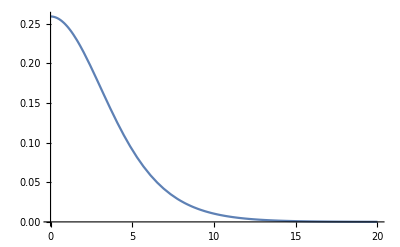

```mathematica
Plot[u0[r],{r,0,20}]
```

```mathematica
Bag2[sin_,δs_,in_,out_,t_,ϵ_,Rin_,n_]:=(
h=Rin/n;
R=Rin;
s=sin;
For[k=in,k≤out,k++,
λ[k]=s;
U[σ_]:=(σ-1)^2(s σ^2+2 t  σ+t );
dU[σ_]:=2 (-3 t+s (1-2 σ)) (1-σ) σ;
(*σ equations*)
eqσ[0]=6(σ[1]-σ[0])==h^2(dU[2/3 σ[0]+1/3 σ[1]]+(2/3 u[0]+1/3 u[1])^2);
Table[eqσ[i]=(1-h/2 2/(i h))σ[i-1]-2 σ[i]+(1 +h/2 2/(i h))σ[i+1]==h^2(dU[1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]]+(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])^2-(-(-u[i-1]/(2h)+u[i+1]/(2h))/(ϵ+1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]))^2),{i,1,n}];
eqσ[n+1]=1/6(σ[n-1]+4σ[n]+σ[n+1])+R/(1+√(2(s+3 t))R)1/(2h)(-σ[n-1]+σ[n+1])==1;
(*u equations*)
equ[0]=6(u[1]-u[0])==h^2((2/3 σ[0]+1/3 σ[1])^2-ϵ^2)(2/3 u[0]+1/3 u[1]);
Table[equ[i]=(1-h/2 2/(i h))u[i-1]-2 u[i]+(1 +h/2 2/(i h))u[i+1]==h^2(((1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1])^2-ϵ^2)(1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])+((-σ[i-1]/(2h)+σ[i+1]/(2h))/(ϵ+1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]))(-u[i-1]/(2h)+u[i+1]/(2h))),{i,1,n}];
equ[n+1]=(1/6(√(1-ϵ^2)+1/R)-1/(2h))u[n-1]+2/3(√(1-ϵ^2)+1/R)u[n]+(1/6(√(1-ϵ^2)+1/R)+1/(2 h))u[n+1]==0;
(*initial approximation for σ*)
Table[σineq[i]=1/6 σin[i-1]+2/3 σin[i]+1/6 σin[i+1]==σ0[i h],{i,0,n}];
σineq[-1]=σin[-1]==σin[1]; σineq[n+1]=σin[n-1]==σin[n+1];
σinappr=(*Table[σin[j],{j,-1,n+1}]/.*)NSolve[Table[σineq[i],{i,-1,n+1}],Table[σin[j],{j,-1,n+1}]];
(*initial approximation for u*)
Table[uineq[i]=1/6 uin[i-1]+2/3 uin[i]+1/6 uin[i+1]==u0[i h],{i,0,n}];
uineq[-1]=uin[-1]==uin[1];uineq[n+1]=uin[n-1]==uin[n+1];
uinappr=(*Table[σin[j],{j,-1,n+1}]/.*)NSolve[Table[uineq[i],{i,-1,n+1}],Table[uin[j],{j,-1,n+1}]];
(*Solver*)
equations=Join[Table[eqσ[i],{i,0,n+1}],Table[equ[i],{i,0,n+1}]];
variables=Join[Table[{σ[i],σin[i]},{i,0,n+1}],Table[{u[i],uin[i]},{i,0,n+1}]]/.σinappr/.uinappr;
sol=FindRoot[equations,variables[[1,1]]];
σprofile=Table[{i h,1/6(σ[i-1]+4 σ[i]+σ[i+1])},{i,0,n}]/.σ[-1]->σ[1]/.sol;
uprofile=Table[{i h,1/6(u[i-1]+4 u[i]+u[i+1])},{i,0,n}]/.u[-1]->u[1]/.sol;
σcoeff[k]=Table[{h i,σ[i]},{i,-1,n+1}]/.σ[-1]->σ[1]/.sol;
ucoeff[k]=Table[{h i,u[i]},{i,-1,n+1}]/.u[-1]->u[1]/.sol;
η[k]=4 π h Sum[(i h)^2((1/6 u[i-1]+2/3 u[i]+1/6 u[i+1])^2+(-(-u[i-1]/(2h)+u[i+1]/(2h))/(ϵ+1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]))^2)/.sol,{i,0,n}];
H[k]=η[k]ϵ+4 π h Sum[(i h)^2(1/2(-(σ[i-1]-σ[i+1])/(2h))^2+U[1/6 σ[i-1]+2/3 σ[i]+1/6 σ[i+1]])/.sol,{i,0,n}];
σ0[x_]:=Piecewise[{{Sum[σ[i]BSplineBasis[{3,{(i-2)h,(i-1)h,i h,(i+1)h,(i+2)h}},0,x],{i,-1,n+1}]/.σ[-1]->σ[1]/.sol,x<R},{1,x≥R}}];
u0[x_]:=Sum[u[i]BSplineBasis[{3,{(i-2)h,(i-1)h,i h,(i+1)h,(i+2)h}},0,x],{i,-1,n+1}]/.u[-1]->u[1]/.sol;
time=1;
While[σprofile[[time,2]]<(1-10^-2),time++];
R=2(time-1)h;
box[k]=R;
h=R/n;
s=sin δs^-k;
]
)
```

```mathematica
(*Bag[sin_,δs_,in_,out_,t_,ϵ0_,Rin_,n_]*)
Bag2[0.01,1.2,1,50,0,0.898,21,400]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

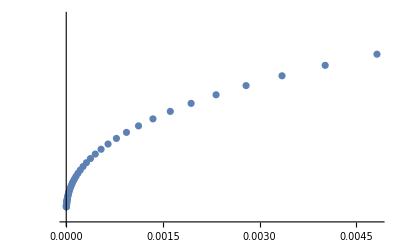

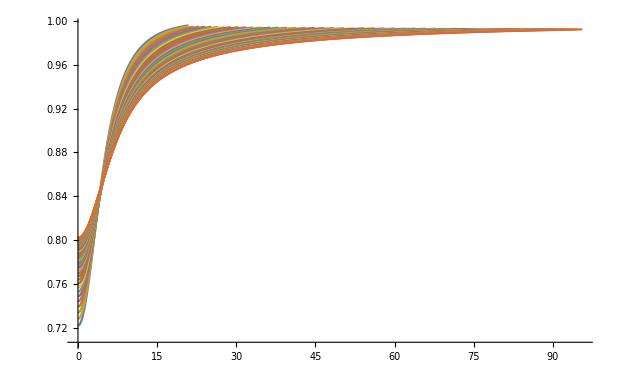

```mathematica
ListLogPlot[Table[{λ[k],η[k]},{k,2,49}]]
ListLinePlot[Table[Table[{σcoeff[k][[i+1,1]],1/6(σcoeff[k][[i,2]]+4σcoeff[k][[i+1,2]]+σcoeff[k][[i+2,2]])},{i,1,400}],{k,1,49}],PlotRange->Full]
```

```mathematica
λ[50]
```

1.31862×10^-6

```mathematica
box[50]
```

97.5576